## Interpolation

```mathematica
Quit
```

```mathematica
Sum[Subscript[a, i]*x0^i,{i,0,4}]
```

a_0+x0 a_1+x0^2 a_2+x0^3 a_3+x0^4 a_4

```mathematica
pol[x0_] :=Subscript[a, 0]+x0 Subscript[a, 1]+x0^2 Subscript[a, 2]+x0^3 Subscript[a, 3]+x0^4 Subscript[a, 4]
```

```mathematica
sysm2 = pol[x0 - 2*h] - ym2;
sysm1 = pol[x0 - h] - ym1;
sys0 = pol [x0]- y0;
sys1 = pol[x0+h] - y1;
sys2 = pol[x0 + 2h] - y2;
sys3 = pol[x0 + 3h] - y3;
sys4 = pol[x0 + 4h] - y4;
```

```mathematica
coeffsc=Solve[{sysm2,sysm1,sys0,sys1,sys2}==0,{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4]}]//Simplify;
pol[x]/.%[[1]]//Simplify;
%/.{x-> x0 + h/2}//Simplify;
CForm[%]
```

(90*y0 + 60*y1 - 5*y2 - 20*ym1 + 3*ym2)/128.

```mathematica
coeffs$0 = Solve[{sys0,sys1,sys2,sys3, sys4}==0,{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4]}]//Simplify;
pol[x]/.%[[1]]//Simplify;
%/.{x-> x0 + h/2}//Simplify;
CForm[%]
```

(35*y0 + 140*y1 - 70*y2 + 28*y3 - 5*y4)/128.

```mathematica
coeffs$m$1 = Solve[{sysm1,sys0,sys1,sys2,sys3}==0,{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4]}]//Simplify;
pol[x]/.%[[1]]//Simplify;
%/.{x-> x0 + h/2}//Simplify;
CForm[%]
```

(60*y0 + 90*y1 - 20*y2 + 3*y3 - 5*ym1)/128.

```mathematica
dpdx[x0_]:= Subscript[a, 1]+2 x0 Subscript[a, 2]+3 x0^2 Subscript[a, 3]+4 x0^3 Subscript[a, 4]
```

```mathematica
dpdx[x0 + h/2]/.coeffsc[[1]]//Simplify
```

(-27 y0+27 y1-y2+ym1)/(24 h)

```mathematica
dpdx[x0 + h/2]/.coeffs$m$1[[1]]//Simplify
```

(-27 y0+27 y1-y2+ym1)/(24 h)

```mathematica
dpdx[x0 + h/2]/.coeffs$0[[1]]//Simplify
```

(-22 y0+17 y1+9 y2-5 y3+y4)/(24 h)

## Compactification

```mathematica
Quit
```

```mathematica
l = 100;
```

```mathematica
r[x_,m_,j_]:= (x^m/(l/j)^(m-1))/(1-(x/l))    ;
```

```mathematica
rp[x_,m_,j_]:= (l (l/j)^(1-m) x^(-1+m) (l m+x-m x))/(l-x)^2;
```

```mathematica
rp[0.01,1,1]//Simplify
```

1.0002

```mathematica
r[x,2,1];
CForm[%];
ToString[%];
StringReplace[%,{"Power"-> "pow"}]
```

pow(x,2)/(l*(1 - x/l))

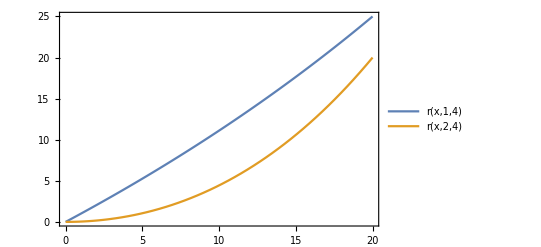

```mathematica
Plot[{r[x,1,4],r[x,2,4]},{x,0,l/5},Frame->True,PlotLegends->"Expressions"]
```

```mathematica
nx = 8000;
```

```mathematica
dx = l/nx//N
```

0.0125

```mathematica
xs = Join[{dx/2,dx}, Subdivide[2*dx,l,nx-2]];
rs[n_,j_]:= Table[r[xs[[m]],n,j],{m,1,Length[xs]-1}]//N
```

```mathematica
rp[dx/2,2,1]
```

0.000125012

```mathematica
rs[1.5,1]
```

{0.0000494137,0.000139772,0.000395384,0.000726457,0.00111859,0.00156348,0.0020555,0.00259055,0.00316544,0.00377761,0.00442495,0.00510566,0.0058182,0.00656125,0.00733361,0.00813424,0.0089622,0.00981663,0.0106968,0.0116019,0.0125313,0.0134845,0.0144609,0.0154599,0.0164811,0.017524,0.0185883,0.0196734,0.020779,0.0219048,0.0230504,0.0242155,0.0253998,0.026603,0.0278249,0.0290651,0.0303234,0.0315995,0.0328934,0.0342046,0.035533,0.0368784,0.0382406,0.0396194,0.0410147,0.0424261,0.0438537,0.0452971,0.0467563,0.0482311,0.0497213,0.0512269,0.0527475,0.0542832,0.0558338,0.0573991,0.0589791,0.0605735,0.0621823,0.0638055,0.0654427,0.067094,0.0687593,0.0704384,0.0721312,0.0738377,0.0755577,0.0772911,0.079038,0.080798,0.0825713,0.0843576,0.0861569,0.0879692,0.0897942,0.0916321,0.0934826,0.0953458,0.0972214,0.0991096,0.10101,0.102923,0.104848,0.106785,0.108735,0.110696,0.11267,0.114655,0.116652,0.118661,0.120682,0.122714,0.124758,0.126814,0.128881,0.13096,0.13305,0.135151,0.137264,0.139388,0.141523,0.14367,0.145827,0.147996,0.150175,0.152366,0.154567,0.156779,0.159002,0.161236,0.163481,0.165736,0.168002,0.170279,0.172566,0.174864,0.177172,0.179491,0.18182,0.184159,0.186509,0.18887,0.19124,0.193621,0.196012,0.198413,0.200824,0.203245,0.205677,0.208118,0.210569,0.213031,0.215502,0.217983,0.220474,0.222975,0.225486,0.228007,0.230537,0.233077,0.235627,0.238186,0.240755,0.243334,0.245922,0.24852,0.251127,0.253744,0.25637,0.259006,0.261651,0.264305,0.266969,0.269643,0.272325,0.275017,0.277718,0.280429,0.283148,0.285877,0.288615,0.291362,0.294118,0.296884,0.299658,0.302442,0.305234,0.308036,0.310847,0.313666,0.316495,0.319332,0.322179,0.325034,0.327898,0.330771,0.333653,0.336544,0.339443,0.342352,0.345269,0.348194,0.351129,0.354072,0.357024,0.359984,0.362954,0.365931,0.368918,0.371913,0.374916,0.377928,0.380949,0.383978,0.387016,0.390062,0.393117,0.39618,0.399252,0.402332,0.40542,0.408517,0.411622,0.414736,0.417858,0.420988,0.424127,0.427273,0.430429,0.433592,0.436764,0.439944,0.443132,0.446328,0.449533,0.452745,0.455966,0.459195,0.462433,0.465678,0.468932,0.472193,0.475463,0.478741,0.482026,0.48532,0.488622,0.491932,0.49525,0.498576,0.50191,0.505252,0.508602,0.511959,0.515325,0.518699,0.522081,0.52547,0.528867,0.532273,0.535686,0.539107,0.542536,0.545972,0.549417,0.552869,0.556329,0.559797,0.563273,0.566756,0.570247,0.573746,0.577253,0.580767,0.58429,0.587819,0.591357,0.594902,0.598455,0.602015,0.605584,0.609159,0.612743,0.616334,0.619933,0.623539,0.627153,0.630774,0.634403,0.63804,0.641684,0.645336,0.648995,0.652662,0.656336,0.660018,0.663707,0.667404,0.671108,0.67482,0.678539,0.682266,0.686,0.689741,0.69349,0.697247,0.70101,0.704782,0.70856,0.712346,0.716139,0.71994,0.723748,0.727564,0.731387,0.735217,0.739054,0.742899,0.746751,0.750611,0.754477,0.758351,0.762233,0.766121,0.770017,0.77392,0.77783,0.781748,0.785673,0.789605,0.793544,0.797491,0.801445,0.805406,0.809374,0.813349,0.817332,0.821321,0.825318,0.829322,0.833333,0.837352,0.841377,0.84541,0.849449,0.853496,0.85755,0.861611,0.86568,0.869755,0.873837,0.877927,0.882023,0.886127,0.890238,0.894355,0.89848,0.902612,0.906751,0.910897,0.91505,0.91921,0.923376,0.92755,0.931731,0.935919,0.940114,0.944316,0.948525,0.952741,0.956964,0.961194,0.965431,0.969674,0.973925,0.978183,0.982447,0.986719,0.990997,0.995283,0.999575,1.00387,1.00818,1.01249,1.01681,1.02114,1.02547,1.02981,1.03416,1.03852,1.04288,1.04724,1.05162,1.056,1.06039,1.06479,1.06919,1.0736,1.07801,1.08244,1.08686,1.0913,1.09574,1.10019,1.10465,1.10911,1.11358,1.11806,1.12255,1.12704,1.13153,1.13604,1.14055,1.14507,1.14959,1.15412,1.15866,1.1632,1.16776,1.17231,1.17688,1.18145,1.18603,1.19061,1.1952,1.1998,1.20441,1.20902,1.21364,1.21826,1.22289,1.22753,1.23218,1.23683,1.24149,1.24615,1.25083,1.2555,1.26019,1.26488,1.26958,1.27428,1.279,1.28371,1.28844,1.29317,1.29791,1.30265,1.3074,1.31216,1.31693,1.3217,1.32648,1.33126,1.33605,1.34085,1.34565,1.35046,1.35528,1.36011,1.36494,1.36977,1.37462,1.37947,1.38432,1.38919,1.39406,1.39893,1.40382,1.4087,1.4136,1.4185,1.42341,1.42833,1.43325,1.43818,1.44311,1.44806,1.453,1.45796,1.46292,1.46789,1.47286,1.47784,1.48283,1.48782,1.49282,1.49783,1.50284,1.50786,1.51289,1.51792,1.52296,1.52801,1.53306,1.53812,1.54318,1.54825,1.55333,1.55841,1.5635,1.5686,1.5737,1.57881,1.58393,1.58905,1.59418,1.59932,1.60446,1.60961,1.61476,1.61993,1.62509,1.63027,1.63545,1.64064,1.64583,1.65103,1.65624,1.66145,1.66667,1.67189,1.67712,1.68236,1.68761,1.69286,1.69811,1.70338,1.70865,1.71393,1.71921,1.7245,1.72979,1.73509,1.7404,1.74572,1.75104,1.75637,1.7617,1.76704,1.77239,1.77774,1.7831,1.78846,1.79384,1.79921,1.8046,1.80999,1.81539,1.82079,1.8262,1.83162,1.83704,1.84247,1.8479,1.85334,1.85879,1.86425,1.86971,1.87517,1.88064,1.88612,1.89161,1.8971,1.9026,1.9081,1.91362,1.91913,1.92466,1.93019,1.93572,1.94126,1.94681,1.95237,1.95793,1.96349,1.96907,1.97465,1.98023,1.98583,1.99143,1.99703,2.00264,2.00826,2.01388,2.01951,2.02515,2.03079,2.03644,2.0421,2.04776,2.05342,2.0591,2.06478,2.07047,2.07616,2.08186,2.08756,2.09327,2.09899,2.10471,2.11044,2.11618,2.12192,2.12767,2.13343,2.13919,2.14495,2.15073,2.15651,2.16229,2.16809,2.17389,2.17969,2.1855,2.19132,2.19714,2.20297,2.20881,2.21465,2.2205,2.22635,2.23221,2.23808,2.24395,2.24983,2.25572,2.26161,2.26751,2.27341,2.27932,2.28524,2.29116,2.29709,2.30302,2.30896,2.31491,2.32087,2.32682,2.33279,2.33876,2.34474,2.35073,2.35672,2.36271,2.36872,2.37473,2.38074,2.38676,2.39279,2.39882,2.40486,2.41091,2.41696,2.42302,2.42909,2.43516,2.44123,2.44732,2.45341,2.4595,2.4656,2.47171,2.47783,2.48395,2.49007,2.4962,2.50234,2.50849,2.51464,2.5208,2.52696,2.53313,2.5393,2.54549,2.55167,2.55787,2.56407,2.57027,2.57649,2.58271,2.58893,2.59516,2.6014,2.60764,2.61389,2.62015,2.62641,2.63267,2.63895,2.64523,2.65151,2.65781,2.66411,2.67041,2.67672,2.68304,2.68936,2.69569,2.70202,2.70837,2.71471,2.72107,2.72743,2.73379,2.74016,2.74654,2.75293,2.75932,2.76571,2.77212,2.77852,2.78494,2.79136,2.79779,2.80422,2.81066,2.8171,2.82356,2.83001,2.83648,2.84295,2.84942,2.8559,2.86239,2.86889,2.87539,2.88189,2.88841,2.89492,2.90145,2.90798,2.91452,2.92106,2.92761,2.93416,2.94073,2.94729,2.95387,2.96045,2.96703,2.97362,2.98022,2.98683,2.99344,3.00005,3.00668,3.0133,3.01994,3.02658,3.03323,3.03988,3.04654,3.0532,3.05988,3.06655,3.07324,3.07993,3.08662,3.09332,3.10003,3.10674,3.11346,3.12019,3.12692,3.13366,3.14041,3.14716,3.15391,3.16067,3.16744,3.17422,3.181,3.18779,3.19458,3.20138,3.20818,3.215,3.22181,3.22864,3.23547,3.2423,3.24914,3.25599,3.26285,3.26971,3.27657,3.28344,3.29032,3.29721,3.3041,3.31099,3.3179,3.32481,3.33172,3.33864,3.34557,3.3525,3.35944,3.36639,3.37334,3.38029,3.38726,3.39423,3.4012,3.40818,3.41517,3.42217,3.42917,3.43617,3.44319,3.4502,3.45723,3.46426,3.47129,3.47834,3.48539,3.49244,3.4995,3.50657,3.51364,3.52072,3.52781,3.5349,3.54199,3.5491,3.55621,3.56332,3.57045,3.57757,3.58471,3.59185,3.59899,3.60614,3.6133,3.62047,3.62764,3.63481,3.642,3.64919,3.65638,3.66358,3.67079,3.678,3.68522,3.69244,3.69968,3.70691,3.71416,3.72141,3.72866,3.73592,3.74319,3.75046,3.75774,3.76503,3.77232,3.77962,3.78693,3.79424,3.80155,3.80887,3.8162,3.82354,3.83088,3.83823,3.84558,3.85294,3.8603,3.86767,3.87505,3.88243,3.88982,3.89722,3.90462,3.91203,3.91944,3.92686,3.93429,3.94172,3.94916,3.9566,3.96405,3.97151,3.97897,3.98644,3.99391,4.0014,4.00888,4.01637,4.02387,4.03138,4.03889,4.04641,4.05393,4.06146,4.069,4.07654,4.08409,4.09164,4.0992,4.10677,4.11434,4.12192,4.1295,4.13709,4.14469,4.15229,4.1599,4.16751,4.17513,4.18276,4.19039,4.19803,4.20568,4.21333,4.22099,4.22865,4.23632,4.244,4.25168,4.25937,4.26706,4.27476,4.28247,4.29018,4.2979,4.30562,4.31335,4.32109,4.32883,4.33658,4.34434,4.3521,4.35987,4.36764,4.37542,4.3832,4.391,4.39879,4.4066,4.41441,4.42222,4.43005,4.43788,4.44571,4.45355,4.4614,4.46925,4.47711,4.48497,4.49285,4.50072,4.50861,4.5165,4.52439,4.53229,4.5402,4.54812,4.55604,4.56396,4.5719,4.57983,4.58778,4.59573,4.60369,4.61165,4.61962,4.62759,4.63557,4.64356,4.65156,4.65956,4.66756,4.67557,4.68359,4.69162,4.69965,4.70768,4.71573,4.72377,4.73183,4.73989,4.74796,4.75603,4.76411,4.7722,4.78029,4.78839,4.79649,4.8046,4.81272,4.82084,4.82897,4.8371,4.84524,4.85339,4.86154,4.8697,4.87787,4.88604,4.89422,4.9024,4.91059,4.91879,4.92699,4.9352,4.94341,4.95163,4.95986,4.96809,4.97633,4.98458,4.99283,5.00109,5.00935,5.01762,5.0259,5.03418,5.04247,5.05076,5.05906,5.06737,5.07568,5.084,5.09233,5.10066,5.109,5.11734,5.12569,5.13405,5.14241,5.15078,5.15915,5.16753,5.17592,5.18431,5.19271,5.20112,5.20953,5.21795,5.22637,5.2348,5.24324,5.25168,5.26013,5.26859,5.27705,5.28551,5.29399,5.30247,5.31095,5.31945,5.32794,5.33645,5.34496,5.35348,5.362,5.37053,5.37906,5.38761,5.39615,5.40471,5.41327,5.42183,5.43041,5.43898,5.44757,5.45616,5.46476,5.47336,5.48197,5.49059,5.49921,5.50784,5.51647,5.52511,5.53376,5.54241,5.55107,5.55974,5.56841,5.57709,5.58577,5.59446,5.60316,5.61186,5.62057,5.62929,5.63801,5.64674,5.65547,5.66421,5.67296,5.68171,5.69047,5.69923,5.708,5.71678,5.72556,5.73435,5.74315,5.75195,5.76076,5.76958,5.7784,5.78723,5.79606,5.8049,5.81374,5.8226,5.83146,5.84032,5.84919,5.85807,5.86695,5.87584,5.88474,5.89364,5.90255,5.91146,5.92038,5.92931,5.93824,5.94718,5.95613,5.96508,5.97404,5.98301,5.99198,6.00095,6.00994,6.01893,6.02792,6.03692,6.04593,6.05495,6.06397,6.073,6.08203,6.09107,6.10012,6.10917,6.11823,6.12729,6.13636,6.14544,6.15452,6.16362,6.17271,6.18181,6.19092,6.20004,6.20916,6.21829,6.22742,6.23656,6.24571,6.25486,6.26402,6.27319,6.28236,6.29154,6.30072,6.30991,6.31911,6.32831,6.33752,6.34674,6.35596,6.36519,6.37442,6.38366,6.39291,6.40216,6.41142,6.42069,6.42996,6.43924,6.44853,6.45782,6.46712,6.47642,6.48573,6.49505,6.50437,6.5137,6.52304,6.53238,6.54173,6.55108,6.56044,6.56981,6.57919,6.58857,6.59795,6.60734,6.61674,6.62615,6.63556,6.64498,6.6544,6.66383,6.67327,6.68272,6.69217,6.70162,6.71108,6.72055,6.73003,6.73951,6.749,6.75849,6.76799,6.7775,6.78701,6.79653,6.80606,6.81559,6.82513,6.83468,6.84423,6.85379,6.86335,6.87292,6.8825,6.89208,6.90167,6.91127,6.92087,6.93048,6.94009,6.94972,6.95934,6.96898,6.97862,6.98827,6.99792,7.00758,7.01725,7.02692,7.0366,7.04629,7.05598,7.06568,7.07538,7.08509,7.09481,7.10453,7.11426,7.124,7.13374,7.14349,7.15325,7.16301,7.17278,7.18256,7.19234,7.20213,7.21192,7.22172,7.23153,7.24134,7.25116,7.26099,7.27082,7.28066,7.29051,7.30036,7.31022,7.32009,7.32996,7.33984,7.34972,7.35961,7.36951,7.37941,7.38932,7.39924,7.40917,7.41909,7.42903,7.43897,7.44892,7.45888,7.46884,7.47881,7.48878,7.49877,7.50875,7.51875,7.52875,7.53876,7.54877,7.55879,7.56882,7.57885,7.58889,7.59894,7.60899,7.61905,7.62911,7.63919,7.64926,7.65935,7.66944,7.67954,7.68964,7.69975,7.70987,7.72,7.73013,7.74026,7.75041,7.76056,7.77071,7.78088,7.79105,7.80122,7.8114,7.82159,7.83179,7.84199,7.8522,7.86241,7.87264,7.88286,7.8931,7.90334,7.91359,7.92384,7.9341,7.94437,7.95464,7.96492,7.97521,7.98551,7.99581,8.00611,8.01642,8.02674,8.03707,8.0474,8.05774,8.06809,8.07844,8.0888,8.09917,8.10954,8.11992,8.1303,8.14069,8.15109,8.1615,8.17191,8.18233,8.19275,8.20318,8.21362,8.22406,8.23451,8.24497,8.25544,8.26591,8.27638,8.28687,8.29736,8.30785,8.31836,8.32887,8.33938,8.34991,8.36044,8.37097,8.38152,8.39207,8.40262,8.41319,8.42376,8.43433,8.44492,8.4555,8.4661,8.4767,8.48731,8.49793,8.50855,8.51918,8.52982,8.54046,8.55111,8.56176,8.57242,8.58309,8.59377,8.60445,8.61514,8.62584,8.63654,8.64725,8.65796,8.66868,8.67941,8.69015,8.70089,8.71164,8.72239,8.73316,8.74392,8.7547,8.76548,8.77627,8.78706,8.79787,8.80868,8.81949,8.83031,8.84114,8.85198,8.86282,8.87367,8.88452,8.89538,8.90625,8.91713,8.92801,8.9389,8.94979,8.9607,8.97161,8.98252,8.99344,9.00437,9.01531,9.02625,9.0372,9.04816,9.05912,9.07009,9.08106,9.09205,9.10304,9.11403,9.12503,9.13604,9.14706,9.15808,9.16911,9.18015,9.19119,9.20224,9.2133,9.22436,9.23543,9.24651,9.25759,9.26868,9.27978,9.29089,9.302,9.31311,9.32424,9.33537,9.34651,9.35765,9.3688,9.37996,9.39113,9.4023,9.41348,9.42466,9.43585,9.44705,9.45826,9.46947,9.48069,9.49191,9.50315,9.51439,9.52563,9.53688,9.54814,9.55941,9.57068,9.58196,9.59325,9.60455,9.61585,9.62715,9.63847,9.64979,9.66112,9.67245,9.68379,9.69514,9.7065,9.71786,9.72923,9.7406,9.75199,9.76338,9.77477,9.78617,9.79758,9.809,9.82042,9.83186,9.84329,9.85474,9.86619,9.87765,9.88911,9.90058,9.91206,9.92355,9.93504,9.94654,9.95804,9.96955,9.98107,9.9926,10.0041,10.0157,10.0272,10.0388,10.0503,10.0619,10.0735,10.0851,10.0966,10.1082,10.1198,10.1315,10.1431,10.1547,10.1663,10.178,10.1896,10.2013,10.2129,10.2246,10.2362,10.2479,10.2596,10.2713,10.283,10.2947,10.3064,10.3181,10.3299,10.3416,10.3533,10.3651,10.3768,10.3886,10.4004,10.4122,10.4239,10.4357,10.4475,10.4593,10.4711,10.483,10.4948,10.5066,10.5184,10.5303,10.5421,10.554,10.5659,10.5777,10.5896,10.6015,10.6134,10.6253,10.6372,10.6491,10.661,10.673,10.6849,10.6969,10.7088,10.7208,10.7327,10.7447,10.7567,10.7687,10.7807,10.7926,10.8047,10.8167,10.8287,10.8407,10.8527,10.8648,10.8768,10.8889,10.901,10.913,10.9251,10.9372,10.9493,10.9614,10.9735,10.9856,10.9977,11.0098,11.022,11.0341,11.0463,11.0584,11.0706,11.0827,11.0949,11.1071,11.1193,11.1315,11.1437,11.1559,11.1681,11.1803,11.1926,11.2048,11.2171,11.2293,11.2416,11.2538,11.2661,11.2784,11.2907,11.303,11.3153,11.3276,11.3399,11.3522,11.3646,11.3769,11.3893,11.4016,11.414,11.4263,11.4387,11.4511,11.4635,11.4759,11.4883,11.5007,11.5131,11.5255,11.538,11.5504,11.5628,11.5753,11.5878,11.6002,11.6127,11.6252,11.6377,11.6502,11.6627,11.6752,11.6877,11.7002,11.7128,11.7253,11.7378,11.7504,11.763,11.7755,11.7881,11.8007,11.8133,11.8259,11.8385,11.8511,11.8637,11.8763,11.889,11.9016,11.9143,11.9269,11.9396,11.9522,11.9649,11.9776,11.9903,12.003,12.0157,12.0284,12.0411,12.0539,12.0666,12.0793,12.0921,12.1048,12.1176,12.1304,12.1432,12.1559,12.1687,12.1815,12.1943,12.2072,12.22,12.2328,12.2456,12.2585,12.2713,12.2842,12.2971,12.3099,12.3228,12.3357,12.3486,12.3615,12.3744,12.3873,12.4003,12.4132,12.4261,12.4391,12.452,12.465,12.478,12.4909,12.5039,12.5169,12.5299,12.5429,12.5559,12.5689,12.582,12.595,12.608,12.6211,12.6341,12.6472,12.6603,12.6734,12.6864,12.6995,12.7126,12.7258,12.7389,12.752,12.7651,12.7783,12.7914,12.8046,12.8177,12.8309,12.8441,12.8572,12.8704,12.8836,12.8968,12.91,12.9233,12.9365,12.9497,12.963,12.9762,12.9895,13.0027,13.016,13.0293,13.0426,13.0559,13.0692,13.0825,13.0958,13.1091,13.1225,13.1358,13.1491,13.1625,13.1759,13.1892,13.2026,13.216,13.2294,13.2428,13.2562,13.2696,13.283,13.2964,13.3099,13.3233,13.3368,13.3502,13.3637,13.3772,13.3907,13.4041,13.4176,13.4311,13.4447,13.4582,13.4717,13.4852,13.4988,13.5123,13.5259,13.5395,13.553,13.5666,13.5802,13.5938,13.6074,13.621,13.6346,13.6482,13.6619,13.6755,13.6892,13.7028,13.7165,13.7302,13.7438,13.7575,13.7712,13.7849,13.7986,13.8123,13.8261,13.8398,13.8535,13.8673,13.881,13.8948,13.9086,13.9223,13.9361,13.9499,13.9637,13.9775,13.9913,14.0052,14.019,14.0328,14.0467,14.0605,14.0744,14.0883,14.1021,14.116,14.1299,14.1438,14.1577,14.1716,14.1856,14.1995,14.2134,14.2274,14.2413,14.2553,14.2693,14.2832,14.2972,14.3112,14.3252,14.3392,14.3532,14.3673,14.3813,14.3953,14.4094,14.4234,14.4375,14.4516,14.4656,14.4797,14.4938,14.5079,14.522,14.5361,14.5503,14.5644,14.5785,14.5927,14.6068,14.621,14.6352,14.6493,14.6635,14.6777,14.6919,14.7061,14.7204,14.7346,14.7488,14.763,14.7773,14.7916,14.8058,14.8201,14.8344,14.8487,14.863,14.8773,14.8916,14.9059,14.9202,14.9345,14.9489,14.9632,14.9776,14.992,15.0063,15.0207,15.0351,15.0495,15.0639,15.0783,15.0927,15.1072,15.1216,15.1361,15.1505,15.165,15.1794,15.1939,15.2084,15.2229,15.2374,15.2519,15.2664,15.2809,15.2955,15.31,15.3246,15.3391,15.3537,15.3682,15.3828,15.3974,15.412,15.4266,15.4412,15.4558,15.4705,15.4851,15.4997,15.5144,15.529,15.5437,15.5584,15.5731,15.5878,15.6025,15.6172,15.6319,15.6466,15.6613,15.6761,15.6908,15.7056,15.7203,15.7351,15.7499,15.7647,15.7795,15.7943,15.8091,15.8239,15.8387,15.8536,15.8684,15.8833,15.8981,15.913,15.9279,15.9427,15.9576,15.9725,15.9874,16.0024,16.0173,16.0322,16.0471,16.0621,16.0771,16.092,16.107,16.122,16.137,16.152,16.167,16.182,16.197,16.212,16.2271,16.2421,16.2572,16.2722,16.2873,16.3024,16.3174,16.3325,16.3476,16.3628,16.3779,16.393,16.4081,16.4233,16.4384,16.4536,16.4687,16.4839,16.4991,16.5143,16.5295,16.5447,16.5599,16.5751,16.5904,16.6056,16.6209,16.6361,16.6514,16.6667,16.6819,16.6972,16.7125,16.7278,16.7432,16.7585,16.7738,16.7892,16.8045,16.8199,16.8352,16.8506,16.866,16.8814,16.8968,16.9122,16.9276,16.943,16.9584,16.9739,16.9893,17.0048,17.0202,17.0357,17.0512,17.0667,17.0822,17.0977,17.1132,17.1287,17.1442,17.1598,17.1753,17.1909,17.2064,17.222,17.2376,17.2532,17.2688,17.2844,17.3,17.3156,17.3313,17.3469,17.3625,17.3782,17.3939,17.4095,17.4252,17.4409,17.4566,17.4723,17.488,17.5037,17.5195,17.5352,17.551,17.5667,17.5825,17.5982,17.614,17.6298,17.6456,17.6614,17.6772,17.6931,17.7089,17.7247,17.7406,17.7564,17.7723,17.7882,17.8041,17.82,17.8358,17.8518,17.8677,17.8836,17.8995,17.9155,17.9314,17.9474,17.9634,17.9793,17.9953,18.0113,18.0273,18.0433,18.0593,18.0754,18.0914,18.1074,18.1235,18.1396,18.1556,18.1717,18.1878,18.2039,18.22,18.2361,18.2522,18.2683,18.2845,18.3006,18.3168,18.333,18.3491,18.3653,18.3815,18.3977,18.4139,18.4301,18.4463,18.4626,18.4788,18.4951,18.5113,18.5276,18.5439,18.5601,18.5764,18.5927,18.6091,18.6254,18.6417,18.658,18.6744,18.6907,18.7071,18.7235,18.7398,18.7562,18.7726,18.789,18.8055,18.8219,18.8383,18.8547,18.8712,18.8877,18.9041,18.9206,18.9371,18.9536,18.9701,18.9866,19.0031,19.0196,19.0362,19.0527,19.0693,19.0858,19.1024,19.119,19.1356,19.1522,19.1688,19.1854,19.202,19.2186,19.2353,19.2519,19.2686,19.2853,19.3019,19.3186,19.3353,19.352,19.3687,19.3855,19.4022,19.4189,19.4357,19.4524,19.4692,19.486,19.5028,19.5195,19.5363,19.5532,19.57,19.5868,19.6036,19.6205,19.6373,19.6542,19.6711,19.6879,19.7048,19.7217,19.7386,19.7556,19.7725,19.7894,19.8064,19.8233,19.8403,19.8572,19.8742,19.8912,19.9082,19.9252,19.9422,19.9592,19.9763,19.9933,20.0104,20.0274,20.0445,20.0616,20.0787,20.0957,20.1129,20.13,20.1471,20.1642,20.1814,20.1985,20.2157,20.2328,20.25,20.2672,20.2844,20.3016,20.3188,20.336,20.3533,20.3705,20.3877,20.405,20.4223,20.4395,20.4568,20.4741,20.4914,20.5087,20.526,20.5434,20.5607,20.5781,20.5954,20.6128,20.6302,20.6475,20.6649,20.6823,20.6998,20.7172,20.7346,20.752,20.7695,20.787,20.8044,20.8219,20.8394,20.8569,20.8744,20.8919,20.9094,20.9269,20.9445,20.962,20.9796,20.9972,21.0147,21.0323,21.0499,21.0675,21.0851,21.1028,21.1204,21.138,21.1557,21.1733,21.191,21.2087,21.2264,21.2441,21.2618,21.2795,21.2972,21.3149,21.3327,21.3504,21.3682,21.386,21.4038,21.4215,21.4393,21.4572,21.475,21.4928,21.5106,21.5285,21.5463,21.5642,21.5821,21.6,21.6178,21.6357,21.6537,21.6716,21.6895,21.7074,21.7254,21.7434,21.7613,21.7793,21.7973,21.8153,21.8333,21.8513,21.8693,21.8874,21.9054,21.9234,21.9415,21.9596,21.9777,21.9957,22.0138,22.032,22.0501,22.0682,22.0863,22.1045,22.1226,22.1408,22.159,22.1772,22.1953,22.2136,22.2318,22.25,22.2682,22.2865,22.3047,22.323,22.3412,22.3595,22.3778,22.3961,22.4144,22.4327,22.4511,22.4694,22.4877,22.5061,22.5245,22.5428,22.5612,22.5796,22.598,22.6164,22.6348,22.6533,22.6717,22.6902,22.7086,22.7271,22.7456,22.7641,22.7826,22.8011,22.8196,22.8381,22.8567,22.8752,22.8938,22.9123,22.9309,22.9495,22.9681,22.9867,23.0053,23.0239,23.0426,23.0612,23.0799,23.0985,23.1172,23.1359,23.1546,23.1733,23.192,23.2107,23.2294,23.2482,23.2669,23.2857,23.3045,23.3232,23.342,23.3608,23.3796,23.3985,23.4173,23.4361,23.455,23.4738,23.4927,23.5116,23.5305,23.5494,23.5683,23.5872,23.6061,23.625,23.644,23.6629,23.6819,23.7009,23.7199,23.7389,23.7579,23.7769,23.7959,23.8149,23.834,23.853,23.8721,23.8912,23.9103,23.9294,23.9485,23.9676,23.9867,24.0058,24.025,24.0441,24.0633,24.0825,24.1017,24.1209,24.1401,24.1593,24.1785,24.1977,24.217,24.2362,24.2555,24.2748,24.294,24.3133,24.3326,24.352,24.3713,24.3906,24.41,24.4293,24.4487,24.468,24.4874,24.5068,24.5262,24.5456,24.5651,24.5845,24.6039,24.6234,24.6429,24.6623,24.6818,24.7013,24.7208,24.7403,24.7599,24.7794,24.7989,24.8185,24.8381,24.8576,24.8772,24.8968,24.9164,24.936,24.9557,24.9753,24.9949,25.0146,25.0343,25.0539,25.0736,25.0933,25.113,25.1327,25.1525,25.1722,25.192,25.2117,25.2315,25.2513,25.2711,25.2909,25.3107,25.3305,25.3503,25.3702,25.39,25.4099,25.4297,25.4496,25.4695,25.4894,25.5093,25.5292,25.5492,25.5691,25.5891,25.609,25.629,25.649,25.669,25.689,25.709,25.729,25.7491,25.7691,25.7892,25.8092,25.8293,25.8494,25.8695,25.8896,25.9097,25.9299,25.95,25.9702,25.9903,26.0105,26.0307,26.0509,26.0711,26.0913,26.1115,26.1317,26.152,26.1722,26.1925,26.2128,26.2331,26.2534,26.2737,26.294,26.3143,26.3346,26.355,26.3754,26.3957,26.4161,26.4365,26.4569,26.4773,26.4977,26.5182,26.5386,26.5591,26.5795,26.6,26.6205,26.641,26.6615,26.682,26.7025,26.7231,26.7436,26.7642,26.7848,26.8053,26.8259,26.8465,26.8672,26.8878,26.9084,26.9291,26.9497,26.9704,26.9911,27.0117,27.0324,27.0532,27.0739,27.0946,27.1153,27.1361,27.1569,27.1776,27.1984,27.2192,27.24,27.2608,27.2817,27.3025,27.3233,27.3442,27.3651,27.386,27.4069,27.4278,27.4487,27.4696,27.4905,27.5115,27.5324,27.5534,27.5744,27.5954,27.6164,27.6374,27.6584,27.6794,27.7005,27.7215,27.7426,27.7637,27.7848,27.8059,27.827,27.8481,27.8692,27.8904,27.9115,27.9327,27.9538,27.975,27.9962,28.0174,28.0386,28.0599,28.0811,28.1024,28.1236,28.1449,28.1662,28.1875,28.2088,28.2301,28.2514,28.2728,28.2941,28.3155,28.3368,28.3582,28.3796,28.401,28.4224,28.4439,28.4653,28.4868,28.5082,28.5297,28.5512,28.5727,28.5942,28.6157,28.6372,28.6587,28.6803,28.7019,28.7234,28.745,28.7666,28.7882,28.8098,28.8314,28.8531,28.8747,28.8964,28.9181,28.9397,28.9614,28.9831,29.0049,29.0266,29.0483,29.0701,29.0918,29.1136,29.1354,29.1572,29.179,29.2008,29.2226,29.2445,29.2663,29.2882,29.3101,29.3319,29.3538,29.3757,29.3977,29.4196,29.4415,29.4635,29.4855,29.5074,29.5294,29.5514,29.5734,29.5954,29.6175,29.6395,29.6616,29.6836,29.7057,29.7278,29.7499,29.772,29.7941,29.8163,29.8384,29.8606,29.8827,29.9049,29.9271,29.9493,29.9715,29.9938,30.016,30.0382,30.0605,30.0828,30.1051,30.1273,30.1497,30.172,30.1943,30.2166,30.239,30.2614,30.2837,30.3061,30.3285,30.3509,30.3733,30.3958,30.4182,30.4407,30.4631,30.4856,30.5081,30.5306,30.5531,30.5757,30.5982,30.6207,30.6433,30.6659,30.6885,30.7111,30.7337,30.7563,30.7789,30.8016,30.8242,30.8469,30.8695,30.8922,30.9149,30.9377,30.9604,30.9831,31.0059,31.0286,31.0514,31.0742,31.097,31.1198,31.1426,31.1654,31.1883,31.2111,31.234,31.2569,31.2797,31.3026,31.3256,31.3485,31.3714,31.3944,31.4173,31.4403,31.4633,31.4863,31.5093,31.5323,31.5553,31.5784,31.6014,31.6245,31.6476,31.6707,31.6938,31.7169,31.74,31.7631,31.7863,31.8095,31.8326,31.8558,31.879,31.9022,31.9254,31.9487,31.9719,31.9952,32.0184,32.0417,32.065,32.0883,32.1116,32.135,32.1583,32.1817,32.205,32.2284,32.2518,32.2752,32.2986,32.3221,32.3455,32.3689,32.3924,32.4159,32.4394,32.4629,32.4864,32.5099,32.5334,32.557,32.5805,32.6041,32.6277,32.6513,32.6749,32.6985,32.7222,32.7458,32.7695,32.7931,32.8168,32.8405,32.8642,32.8879,32.9117,32.9354,32.9592,32.9829,33.0067,33.0305,33.0543,33.0781,33.1019,33.1258,33.1496,33.1735,33.1974,33.2213,33.2452,33.2691,33.293,33.317,33.3409,33.3649,33.3889,33.4128,33.4368,33.4609,33.4849,33.5089,33.533,33.557,33.5811,33.6052,33.6293,33.6534,33.6775,33.7017,33.7258,33.75,33.7742,33.7984,33.8226,33.8468,33.871,33.8952,33.9195,33.9438,33.968,33.9923,34.0166,34.0409,34.0653,34.0896,34.114,34.1383,34.1627,34.1871,34.2115,34.2359,34.2603,34.2848,34.3092,34.3337,34.3582,34.3827,34.4072,34.4317,34.4562,34.4808,34.5053,34.5299,34.5545,34.579,34.6036,34.6283,34.6529,34.6775,34.7022,34.7269,34.7515,34.7762,34.8009,34.8257,34.8504,34.8751,34.8999,34.9247,34.9495,34.9743,34.9991,35.0239,35.0487,35.0736,35.0984,35.1233,35.1482,35.1731,35.198,35.2229,35.2479,35.2728,35.2978,35.3228,35.3478,35.3728,35.3978,35.4228,35.4478,35.4729,35.498,35.523,35.5481,35.5732,35.5984,35.6235,35.6486,35.6738,35.699,35.7242,35.7494,35.7746,35.7998,35.825,35.8503,35.8755,35.9008,35.9261,35.9514,35.9767,36.0021,36.0274,36.0528,36.0781,36.1035,36.1289,36.1543,36.1797,36.2052,36.2306,36.2561,36.2815,36.307,36.3325,36.358,36.3836,36.4091,36.4347,36.4602,36.4858,36.5114,36.537,36.5626,36.5883,36.6139,36.6396,36.6652,36.6909,36.7166,36.7423,36.7681,36.7938,36.8196,36.8453,36.8711,36.8969,36.9227,36.9485,36.9744,37.0002,37.0261,37.0519,37.0778,37.1037,37.1296,37.1556,37.1815,37.2075,37.2334,37.2594,37.2854,37.3114,37.3374,37.3635,37.3895,37.4156,37.4417,37.4678,37.4939,37.52,37.5461,37.5723,37.5984,37.6246,37.6508,37.677,37.7032,37.7294,37.7556,37.7819,37.8082,37.8344,37.8607,37.887,37.9134,37.9397,37.966,37.9924,38.0188,38.0452,38.0716,38.098,38.1244,38.1509,38.1773,38.2038,38.2303,38.2568,38.2833,38.3098,38.3364,38.3629,38.3895,38.4161,38.4427,38.4693,38.4959,38.5225,38.5492,38.5759,38.6025,38.6292,38.6559,38.6827,38.7094,38.7362,38.7629,38.7897,38.8165,38.8433,38.8701,38.8969,38.9238,38.9506,38.9775,39.0044,39.0313,39.0582,39.0852,39.1121,39.1391,39.166,39.193,39.22,39.247,39.2741,39.3011,39.3282,39.3552,39.3823,39.4094,39.4366,39.4637,39.4908,39.518,39.5451,39.5723,39.5995,39.6267,39.654,39.6812,39.7085,39.7357,39.763,39.7903,39.8176,39.845,39.8723,39.8997,39.927,39.9544,39.9818,40.0092,40.0367,40.0641,40.0916,40.119,40.1465,40.174,40.2015,40.2291,40.2566,40.2842,40.3117,40.3393,40.3669,40.3945,40.4222,40.4498,40.4775,40.5051,40.5328,40.5605,40.5882,40.616,40.6437,40.6715,40.6992,40.727,40.7548,40.7826,40.8105,40.8383,40.8662,40.8941,40.922,40.9499,40.9778,41.0057,41.0337,41.0616,41.0896,41.1176,41.1456,41.1736,41.2017,41.2297,41.2578,41.2859,41.314,41.3421,41.3702,41.3983,41.4265,41.4547,41.4828,41.511,41.5392,41.5675,41.5957,41.624,41.6523,41.6805,41.7088,41.7372,41.7655,41.7938,41.8222,41.8506,41.879,41.9074,41.9358,41.9642,41.9927,42.0211,42.0496,42.0781,42.1066,42.1352,42.1637,42.1923,42.2208,42.2494,42.278,42.3066,42.3353,42.3639,42.3926,42.4212,42.4499,42.4786,42.5074,42.5361,42.5649,42.5936,42.6224,42.6512,42.68,42.7088,42.7377,42.7665,42.7954,42.8243,42.8532,42.8821,42.911,42.94,42.969,42.9979,43.0269,43.0559,43.085,43.114,43.1431,43.1721,43.2012,43.2303,43.2594,43.2886,43.3177,43.3469,43.3761,43.4053,43.4345,43.4637,43.4929,43.5222,43.5514,43.5807,43.61,43.6394,43.6687,43.698,43.7274,43.7568,43.7862,43.8156,43.845,43.8744,43.9039,43.9334,43.9629,43.9924,44.0219,44.0514,44.081,44.1105,44.1401,44.1697,44.1993,44.2289,44.2586,44.2882,44.3179,44.3476,44.3773,44.407,44.4368,44.4665,44.4963,44.5261,44.5559,44.5857,44.6155,44.6454,44.6752,44.7051,44.735,44.7649,44.7948,44.8248,44.8547,44.8847,44.9147,44.9447,44.9747,45.0048,45.0348,45.0649,45.095,45.1251,45.1552,45.1853,45.2155,45.2456,45.2758,45.306,45.3362,45.3664,45.3967,45.4269,45.4572,45.4875,45.5178,45.5481,45.5785,45.6088,45.6392,45.6696,45.7,45.7304,45.7609,45.7913,45.8218,45.8523,45.8828,45.9133,45.9438,45.9744,46.0049,46.0355,46.0661,46.0967,46.1274,46.158,46.1887,46.2194,46.2501,46.2808,46.3115,46.3422,46.373,46.4038,46.4346,46.4654,46.4962,46.5271,46.5579,46.5888,46.6197,46.6506,46.6815,46.7125,46.7434,46.7744,46.8054,46.8364,46.8674,46.8984,46.9295,46.9606,46.9917,47.0228,47.0539,47.085,47.1162,47.1474,47.1785,47.2098,47.241,47.2722,47.3035,47.3347,47.366,47.3973,47.4287,47.46,47.4914,47.5227,47.5541,47.5855,47.6169,47.6484,47.6798,47.7113,47.7428,47.7743,47.8058,47.8374,47.8689,47.9005,47.9321,47.9637,47.9953,48.027,48.0586,48.0903,48.122,48.1537,48.1854,48.2172,48.2489,48.2807,48.3125,48.3443,48.3761,48.408,48.4398,48.4717,48.5036,48.5355,48.5674,48.5994,48.6313,48.6633,48.6953,48.7273,48.7594,48.7914,48.8235,48.8556,48.8877,48.9198,48.9519,48.9841,49.0162,49.0484,49.0806,49.1128,49.1451,49.1773,49.2096,49.2419,49.2742,49.3065,49.3389,49.3712,49.4036,49.436,49.4684,49.5008,49.5333,49.5657,49.5982,49.6307,49.6632,49.6958,49.7283,49.7609,49.7935,49.8261,49.8587,49.8913,49.924,49.9566,49.9893,50.022,50.0548,50.0875,50.1203,50.153,50.1858,50.2186,50.2515,50.2843,50.3172,50.3501,50.383,50.4159,50.4488,50.4818,50.5147,50.5477,50.5807,50.6138,50.6468,50.6799,50.7129,50.746,50.7792,50.8123,50.8454,50.8786,50.9118,50.945,50.9782,51.0114,51.0447,51.078,51.1113,51.1446,51.1779,51.2112,51.2446,51.278,51.3114,51.3448,51.3782,51.4117,51.4452,51.4787,51.5122,51.5457,51.5792,51.6128,51.6464,51.68,51.7136,51.7472,51.7809,51.8145,51.8482,51.8819,51.9157,51.9494,51.9832,52.0169,52.0507,52.0846,52.1184,52.1522,52.1861,52.22,52.2539,52.2878,52.3218,52.3557,52.3897,52.4237,52.4577,52.4918,52.5258,52.5599,52.594,52.6281,52.6622,52.6964,52.7305,52.7647,52.7989,52.8331,52.8674,52.9016,52.9359,52.9702,53.0045,53.0388,53.0732,53.1076,53.142,53.1764,53.2108,53.2452,53.2797,53.3142,53.3487,53.3832,53.4177,53.4523,53.4869,53.5214,53.5561,53.5907,53.6253,53.66,53.6947,53.7294,53.7641,53.7989,53.8336,53.8684,53.9032,53.938,53.9729,54.0077,54.0426,54.0775,54.1124,54.1473,54.1823,54.2173,54.2522,54.2872,54.3223,54.3573,54.3924,54.4275,54.4626,54.4977,54.5328,54.568,54.6032,54.6384,54.6736,54.7088,54.7441,54.7794,54.8147,54.85,54.8853,54.9207,54.956,54.9914,55.0268,55.0623,55.0977,55.1332,55.1687,55.2042,55.2397,55.2752,55.3108,55.3464,55.382,55.4176,55.4533,55.4889,55.5246,55.5603,55.596,55.6318,55.6675,55.7033,55.7391,55.7749,55.8108,55.8466,55.8825,55.9184,55.9543,55.9902,56.0262,56.0622,56.0982,56.1342,56.1702,56.2063,56.2423,56.2784,56.3145,56.3507,56.3868,56.423,56.4592,56.4954,56.5316,56.5679,56.6042,56.6405,56.6768,56.7131,56.7494,56.7858,56.8222,56.8586,56.895,56.9315,56.968,57.0045,57.041,57.0775,57.1141,57.1506,57.1872,57.2238,57.2605,57.2971,57.3338,57.3705,57.4072,57.4439,57.4807,57.5174,57.5542,57.591,57.6279,57.6647,57.7016,57.7385,57.7754,57.8123,57.8493,57.8863,57.9233,57.9603,57.9973,58.0344,58.0714,58.1085,58.1457,58.1828,58.22,58.2571,58.2943,58.3315,58.3688,58.4061,58.4433,58.4806,58.518,58.5553,58.5927,58.63,58.6674,58.7049,58.7423,58.7798,58.8173,58.8548,58.8923,58.9299,58.9674,59.005,59.0426,59.0803,59.1179,59.1556,59.1933,59.231,59.2687,59.3065,59.3443,59.3821,59.4199,59.4577,59.4956,59.5335,59.5714,59.6093,59.6472,59.6852,59.7232,59.7612,59.7992,59.8373,59.8754,59.9134,59.9516,59.9897,60.0279,60.066,60.1042,60.1424,60.1807,60.2189,60.2572,60.2955,60.3339,60.3722,60.4106,60.449,60.4874,60.5258,60.5643,60.6027,60.6412,60.6797,60.7183,60.7568,60.7954,60.834,60.8727,60.9113,60.95,60.9887,61.0274,61.0661,61.1049,61.1436,61.1824,61.2212,61.2601,61.2989,61.3378,61.3767,61.4157,61.4546,61.4936,61.5326,61.5716,61.6106,61.6497,61.6887,61.7278,61.767,61.8061,61.8453,61.8845,61.9237,61.9629,62.0022,62.0414,62.0807,62.12,62.1594,62.1987,62.2381,62.2775,62.317,62.3564,62.3959,62.4354,62.4749,62.5144,62.554,62.5936,62.6332,62.6728,62.7125,62.7521,62.7918,62.8315,62.8713,62.911,62.9508,62.9906,63.0304,63.0703,63.1102,63.1501,63.19,63.2299,63.2699,63.3099,63.3499,63.3899,63.4299,63.47,63.5101,63.5502,63.5904,63.6305,63.6707,63.7109,63.7512,63.7914,63.8317,63.872,63.9123,63.9526,63.993,64.0334,64.0738,64.1142,64.1547,64.1952,64.2357,64.2762,64.3168,64.3573,64.3979,64.4385,64.4792,64.5198,64.5605,64.6012,64.642,64.6827,64.7235,64.7643,64.8051,64.846,64.8868,64.9277,64.9686,65.0096,65.0505,65.0915,65.1325,65.1736,65.2146,65.2557,65.2968,65.3379,65.3791,65.4202,65.4614,65.5026,65.5439,65.5851,65.6264,65.6677,65.7091,65.7504,65.7918,65.8332,65.8746,65.9161,65.9575,65.999,66.0406,66.0821,66.1237,66.1653,66.2069,66.2485,66.2902,66.3318,66.3736,66.4153,66.457,66.4988,66.5406,66.5825,66.6243,66.6662,66.7081,66.75,66.7919,66.8339,66.8759,66.9179,66.96,67.002,67.0441,67.0862,67.1284,67.1705,67.2127,67.2549,67.2971,67.3394,67.3817,67.424,67.4663,67.5087,67.551,67.5934,67.6358,67.6783,67.7208,67.7633,67.8058,67.8483,67.8909,67.9335,67.9761,68.0188,68.0614,68.1041,68.1468,68.1896,68.2323,68.2751,68.3179,68.3608,68.4036,68.4465,68.4894,68.5324,68.5753,68.6183,68.6613,68.7043,68.7474,68.7905,68.8336,68.8767,68.9199,68.963,69.0062,69.0495,69.0927,69.136,69.1793,69.2226,69.266,69.3094,69.3528,69.3962,69.4397,69.4831,69.5266,69.5702,69.6137,69.6573,69.7009,69.7445,69.7882,69.8319,69.8756,69.9193,69.963,70.0068,70.0506,70.0944,70.1383,70.1822,70.2261,70.27,70.314,70.3579,70.4019,70.446,70.49,70.5341,70.5782,70.6223,70.6665,70.7107,70.7549,70.7991,70.8434,70.8877,70.932,70.9763,71.0207,71.065,71.1095,71.1539,71.1984,71.2428,71.2874,71.3319,71.3765,71.4211,71.4657,71.5103,71.555,71.5997,71.6444,71.6891,71.7339,71.7787,71.8235,71.8684,71.9132,71.9581,72.0031,72.048,72.093,72.138,72.183,72.2281,72.2732,72.3183,72.3634,72.4086,72.4538,72.499,72.5442,72.5895,72.6348,72.6801,72.7254,72.7708,72.8162,72.8616,72.9071,72.9525,72.998,73.0436,73.0891,73.1347,73.1803,73.226,73.2716,73.3173,73.363,73.4088,73.4545,73.5003,73.5461,73.592,73.6378,73.6837,73.7297,73.7756,73.8216,73.8676,73.9136,73.9597,74.0058,74.0519,74.098,74.1442,74.1904,74.2366,74.2829,74.3292,74.3755,74.4218,74.4681,74.5145,74.5609,74.6074,74.6538,74.7003,74.7468,74.7934,74.84,74.8866,74.9332,74.9798,75.0265,75.0732,75.12,75.1667,75.2135,75.2603,75.3072,75.3541,75.401,75.4479,75.4948,75.5418,75.5888,75.6359,75.6829,75.73,75.7772,75.8243,75.8715,75.9187,75.9659,76.0132,76.0605,76.1078,76.1551,76.2025,76.2499,76.2973,76.3448,76.3922,76.4397,76.4873,76.5348,76.5824,76.6301,76.6777,76.7254,76.7731,76.8208,76.8686,76.9164,76.9642,77.012,77.0599,77.1078,77.1557,77.2037,77.2517,77.2997,77.3477,77.3958,77.4439,77.492,77.5402,77.5884,77.6366,77.6848,77.7331,77.7814,77.8297,77.8781,77.9265,77.9749,78.0233,78.0718,78.1203,78.1688,78.2174,78.2659,78.3146,78.3632,78.4119,78.4606,78.5093,78.5581,78.6068,78.6557,78.7045,78.7534,78.8023,78.8512,78.9002,78.9491,78.9982,79.0472,79.0963,79.1454,79.1945,79.2437,79.2929,79.3421,79.3913,79.4406,79.4899,79.5393,79.5886,79.638,79.6875,79.7369,79.7864,79.8359,79.8855,79.935,79.9846,80.0343,80.0839,80.1336,80.1833,80.2331,80.2829,80.3327,80.3825,80.4324,80.4823,80.5322,80.5822,80.6322,80.6822,80.7322,80.7823,80.8324,80.8825,80.9327,80.9829,81.0331,81.0834,81.1337,81.184,81.2343,81.2847,81.3351,81.3856,81.436,81.4865,81.5371,81.5876,81.6382,81.6888,81.7395,81.7901,81.8409,81.8916,81.9424,81.9932,82.044,82.0949,82.1457,82.1967,82.2476,82.2986,82.3496,82.4007,82.4517,82.5028,82.554,82.6052,82.6564,82.7076,82.7588,82.8101,82.8615,82.9128,82.9642,83.0156,83.067,83.1185,83.17,83.2216,83.2731,83.3247,83.3764,83.428,83.4797,83.5314,83.5832,83.635,83.6868,83.7387,83.7905,83.8424,83.8944,83.9464,83.9984,84.0504,84.1025,84.1546,84.2067,84.2589,84.3111,84.3633,84.4155,84.4678,84.5202,84.5725,84.6249,84.6773,84.7298,84.7822,84.8347,84.8873,84.9399,84.9925,85.0451,85.0978,85.1505,85.2032,85.256,85.3088,85.3616,85.4145,85.4674,85.5203,85.5732,85.6262,85.6793,85.7323,85.7854,85.8385,85.8917,85.9449,85.9981,86.0513,86.1046,86.1579,86.2113,86.2646,86.318,86.3715,86.425,86.4785,86.532,86.5856,86.6392,86.6928,86.7465,86.8002,86.8539,86.9077,86.9615,87.0154,87.0692,87.1231,87.1771,87.231,87.285,87.3391,87.3931,87.4472,87.5014,87.5555,87.6097,87.664,87.7182,87.7725,87.8268,87.8812,87.9356,87.99,88.0445,88.099,88.1535,88.2081,88.2627,88.3173,88.372,88.4267,88.4814,88.5362,88.591,88.6458,88.7007,88.7556,88.8105,88.8655,88.9205,88.9755,89.0306,89.0857,89.1408,89.196,89.2512,89.3064,89.3617,89.417,89.4724,89.5277,89.5831,89.6386,89.6941,89.7496,89.8051,89.8607,89.9163,89.972,90.0276,90.0834,90.1391,90.1949,90.2507,90.3066,90.3625,90.4184,90.4743,90.5303,90.5864,90.6424,90.6985,90.7547,90.8108,90.867,90.9233,90.9795,91.0358,91.0922,91.1485,91.205,91.2614,91.3179,91.3744,91.4309,91.4875,91.5442,91.6008,91.6575,91.7142,91.771,91.8278,91.8846,91.9415,91.9984,92.0553,92.1123,92.1693,92.2263,92.2834,92.3405,92.3977,92.4549,92.5121,92.5693,92.6266,92.684,92.7413,92.7987,92.8562,92.9136,92.9711,93.0287,93.0863,93.1439,93.2015,93.2592,93.3169,93.3747,93.4325,93.4903,93.5482,93.6061,93.664,93.722,93.78,93.8381,93.8962,93.9543,94.0124,94.0706,94.1289,94.1871,94.2454,94.3038,94.3621,94.4206,94.479,94.5375,94.596,94.6546,94.7132,94.7718,94.8305,94.8892,94.9479,95.0067,95.0655,95.1244,95.1833,95.2422,95.3012,95.3602,95.4192,95.4783,95.5374,95.5965,95.6557,95.7149,95.7742,95.8335,95.8928,95.9522,96.0116,96.0711,96.1306,96.1901,96.2497,96.3093,96.3689,96.4286,96.4883,96.548,96.6078,96.6676,96.7275,96.7874,96.8474,96.9073,96.9673,97.0274,97.0875,97.1476,97.2078,97.268,97.3282,97.3885,97.4488,97.5092,97.5696,97.63,97.6905,97.751,97.8116,97.8722,97.9328,97.9934,98.0541,98.1149,98.1757,98.2365,98.2973,98.3582,98.4192,98.4802,98.5412,98.6022,98.6633,98.7244,98.7856,98.8468,98.9081,98.9693,99.0307,99.092,99.1534,99.2149,99.2764,99.3379,99.3994,99.461,99.5227,99.5844,99.6461,99.7078,99.7696,99.8315,99.8933,99.9553,100.017,100.079,100.141,100.203,100.265,100.328,100.39,100.452,100.514,100.577,100.639,100.701,100.764,100.826,100.889,100.951,101.014,101.077,101.139,101.202,101.265,101.327,101.39,101.453,101.516,101.579,101.642,101.705,101.768,101.831,101.894,101.958,102.021,102.084,102.147,102.211,102.274,102.338,102.401,102.465,102.528,102.592,102.655,102.719,102.783,102.847,102.91,102.974,103.038,103.102,103.166,103.23,103.294,103.358,103.422,103.487,103.551,103.615,103.679,103.744,103.808,103.873,103.937,104.002,104.066,104.131,104.195,104.26,104.325,104.39,104.454,104.519,104.584,104.649,104.714,104.779,104.844,104.909,104.974,105.04,105.105,105.17,105.236,105.301,105.366,105.432,105.497,105.563,105.628,105.694,105.76,105.825,105.891,105.957,106.023,106.089,106.155,106.22,106.286,106.353,106.419,106.485,106.551,106.617,106.683,106.75,106.816,106.882,106.949,107.015,107.082,107.148,107.215,107.282,107.348,107.415,107.482,107.549,107.616,107.683,107.75,107.817,107.884,107.951,108.018,108.085,108.152,108.22,108.287,108.354,108.422,108.489,108.557,108.624,108.692,108.759,108.827,108.895,108.963,109.03,109.098,109.166,109.234,109.302,109.37,109.438,109.506,109.574,109.643,109.711,109.779,109.848,109.916,109.984,110.053,110.121,110.19,110.259,110.327,110.396,110.465,110.534,110.602,110.671,110.74,110.809,110.878,110.947,111.016,111.086,111.155,111.224,111.293,111.363,111.432,111.502,111.571,111.641,111.71,111.78,111.85,111.919,111.989,112.059,112.129,112.199,112.269,112.339,112.409,112.479,112.549,112.619,112.689,112.76,112.83,112.9,112.971,113.041,113.112,113.182,113.253,113.324,113.394,113.465,113.536,113.607,113.678,113.749,113.82,113.891,113.962,114.033,114.104,114.175,114.247,114.318,114.389,114.461,114.532,114.604,114.675,114.747,114.819,114.89,114.962,115.034,115.106,115.178,115.25,115.322,115.394,115.466,115.538,115.61,115.682,115.755,115.827,115.899,115.972,116.044,116.117,116.19,116.262,116.335,116.408,116.48,116.553,116.626,116.699,116.772,116.845,116.918,116.991,117.064,117.138,117.211,117.284,117.358,117.431,117.505,117.578,117.652,117.725,117.799,117.873,117.947,118.02,118.094,118.168,118.242,118.316,118.39,118.465,118.539,118.613,118.687,118.762,118.836,118.91,118.985,119.059,119.134,119.209,119.283,119.358,119.433,119.508,119.583,119.658,119.733,119.808,119.883,119.958,120.033,120.108,120.184,120.259,120.335,120.41,120.486,120.561,120.637,120.712,120.788,120.864,120.94,121.016,121.092,121.168,121.244,121.32,121.396,121.472,121.548,121.625,121.701,121.777,121.854,121.93,122.007,122.084,122.16,122.237,122.314,122.391,122.468,122.544,122.621,122.699,122.776,122.853,122.93,123.007,123.085,123.162,123.239,123.317,123.394,123.472,123.55,123.627,123.705,123.783,123.861,123.939,124.017,124.095,124.173,124.251,124.329,124.407,124.485,124.564,124.642,124.721,124.799,124.878,124.956,125.035,125.114,125.193,125.271,125.35,125.429,125.508,125.587,125.666,125.746,125.825,125.904,125.983,126.063,126.142,126.222,126.301,126.381,126.461,126.54,126.62,126.7,126.78,126.86,126.94,127.02,127.1,127.18,127.26,127.341,127.421,127.501,127.582,127.662,127.743,127.824,127.904,127.985,128.066,128.147,128.228,128.309,128.39,128.471,128.552,128.633,128.714,128.796,128.877,128.958,129.04,129.121,129.203,129.285,129.366,129.448,129.53,129.612,129.694,129.776,129.858,129.94,130.022,130.104,130.187,130.269,130.351,130.434,130.517,130.599,130.682,130.764,130.847,130.93,131.013,131.096,131.179,131.262,131.345,131.428,131.511,131.595,131.678,131.762,131.845,131.929,132.012,132.096,132.18,132.263,132.347,132.431,132.515,132.599,132.683,132.767,132.851,132.936,133.02,133.104,133.189,133.273,133.358,133.443,133.527,133.612,133.697,133.782,133.867,133.952,134.037,134.122,134.207,134.292,134.377,134.463,134.548,134.634,134.719,134.805,134.89,134.976,135.062,135.148,135.234,135.32,135.406,135.492,135.578,135.664,135.751,135.837,135.923,136.01,136.096,136.183,136.27,136.356,136.443,136.53,136.617,136.704,136.791,136.878,136.965,137.052,137.14,137.227,137.314,137.402,137.489,137.577,137.665,137.752,137.84,137.928,138.016,138.104,138.192,138.28,138.368,138.457,138.545,138.633,138.722,138.81,138.899,138.988,139.076,139.165,139.254,139.343,139.432,139.521,139.61,139.699,139.788,139.877,139.967,140.056,140.146,140.235,140.325,140.415,140.504,140.594,140.684,140.774,140.864,140.954,141.044,141.134,141.225,141.315,141.405,141.496,141.587,141.677,141.768,141.859,141.949,142.04,142.131,142.222,142.313,142.404,142.496,142.587,142.678,142.77,142.861,142.953,143.044,143.136,143.228,143.32,143.412,143.504,143.596,143.688,143.78,143.872,143.964,144.057,144.149,144.242,144.334,144.427,144.52,144.612,144.705,144.798,144.891,144.984,145.077,145.171,145.264,145.357,145.451,145.544,145.638,145.731,145.825,145.919,146.013,146.107,146.201,146.295,146.389,146.483,146.577,146.671,146.766,146.86,146.955,147.049,147.144,147.239,147.334,147.429,147.524,147.619,147.714,147.809,147.904,147.999,148.095,148.19,148.286,148.381,148.477,148.573,148.669,148.765,148.861,148.957,149.053,149.149,149.245,149.342,149.438,149.534,149.631,149.728,149.824,149.921,150.018,150.115,150.212,150.309,150.406,150.503,150.601,150.698,150.795,150.893,150.991,151.088,151.186,151.284,151.382,151.48,151.578,151.676,151.774,151.872,151.97,152.069,152.167,152.266,152.365,152.463,152.562,152.661,152.76,152.859,152.958,153.057,153.156,153.256,153.355,153.454,153.554,153.654,153.753,153.853,153.953,154.053,154.153,154.253,154.353,154.453,154.554,154.654,154.755,154.855,154.956,155.056,155.157,155.258,155.359,155.46,155.561,155.662,155.763,155.865,155.966,156.068,156.169,156.271,156.372,156.474,156.576,156.678,156.78,156.882,156.984,157.087,157.189,157.291,157.394,157.497,157.599,157.702,157.805,157.908,158.011,158.114,158.217,158.32,158.423,158.527,158.63,158.734,158.837,158.941,159.045,159.149,159.253,159.357,159.461,159.565,159.669,159.774,159.878,159.983,160.087,160.192,160.297,160.401,160.506,160.611,160.716,160.822,160.927,161.032,161.138,161.243,161.349,161.454,161.56,161.666,161.772,161.878,161.984,162.09,162.196,162.303,162.409,162.516,162.622,162.729,162.836,162.943,163.049,163.157,163.264,163.371,163.478,163.585,163.693,163.8,163.908,164.016,164.123,164.231,164.339,164.447,164.555,164.664,164.772,164.88,164.989,165.097,165.206,165.315,165.423,165.532,165.641,165.75,165.859,165.969,166.078,166.187,166.297,166.407,166.516,166.626,166.736,166.846,166.956,167.066,167.176,167.286,167.397,167.507,167.618,167.728,167.839,167.95,168.061,168.172,168.283,168.394,168.505,168.617,168.728,168.84,168.951,169.063,169.175,169.287,169.399,169.511,169.623,169.735,169.848,169.96,170.073,170.185,170.298,170.411,170.524,170.637,170.75,170.863,170.976,171.089,171.203,171.316,171.43,171.544,171.658,171.772,171.886,172.,172.114,172.228,172.342,172.457,172.571,172.686,172.801,172.916,173.031,173.146,173.261,173.376,173.491,173.607,173.722,173.838,173.953,174.069,174.185,174.301,174.417,174.533,174.649,174.766,174.882,174.999,175.115,175.232,175.349,175.466,175.583,175.7,175.817,175.934,176.052,176.169,176.287,176.404,176.522,176.64,176.758,176.876,176.994,177.113,177.231,177.349,177.468,177.587,177.705,177.824,177.943,178.062,178.181,178.301,178.42,178.539,178.659,178.779,178.898,179.018,179.138,179.258,179.378,179.498,179.619,179.739,179.86,179.98,180.101,180.222,180.343,180.464,180.585,180.706,180.828,180.949,181.071,181.192,181.314,181.436,181.558,181.68,181.802,181.924,182.047,182.169,182.292,182.414,182.537,182.66,182.783,182.906,183.029,183.153,183.276,183.399,183.523,183.647,183.77,183.894,184.018,184.142,184.267,184.391,184.515,184.64,184.765,184.889,185.014,185.139,185.264,185.389,185.515,185.64,185.766,185.891,186.017,186.143,186.268,186.395,186.521,186.647,186.773,186.9,187.026,187.153,187.28,187.406,187.533,187.661,187.788,187.915,188.042,188.17,188.298,188.425,188.553,188.681,188.809,188.937,189.066,189.194,189.323,189.451,189.58,189.709,189.838,189.967,190.096,190.225,190.354,190.484,190.614,190.743,190.873,191.003,191.133,191.263,191.394,191.524,191.654,191.785,191.916,192.047,192.178,192.309,192.44,192.571,192.702,192.834,192.966,193.097,193.229,193.361,193.493,193.625,193.758,193.89,194.023,194.155,194.288,194.421,194.554,194.687,194.82,194.954,195.087,195.221,195.354,195.488,195.622,195.756,195.89,196.025,196.159,196.293,196.428,196.563,196.698,196.833,196.968,197.103,197.238,197.374,197.509,197.645,197.781,197.917,198.053,198.189,198.325,198.462,198.598,198.735,198.872,199.008,199.145,199.283,199.42,199.557,199.695,199.832,199.97,200.108,200.246,200.384,200.522,200.66,200.799,200.937,201.076,201.215,201.354,201.493,201.632,201.771,201.911,202.05,202.19,202.33,202.47,202.61,202.75,202.89,203.031,203.171,203.312,203.453,203.594,203.735,203.876,204.017,204.159,204.3,204.442,204.584,204.726,204.868,205.01,205.152,205.295,205.437,205.58,205.723,205.866,206.009,206.152,206.295,206.439,206.582,206.726,206.87,207.014,207.158,207.302,207.447,207.591,207.736,207.881,208.025,208.171,208.316,208.461,208.606,208.752,208.898,209.043,209.189,209.335,209.482,209.628,209.774,209.921,210.068,210.215,210.362,210.509,210.656,210.803,210.951,211.099,211.246,211.394,211.542,211.691,211.839,211.987,212.136,212.285,212.434,212.583,212.732,212.881,213.03,213.18,213.33,213.479,213.629,213.78,213.93,214.08,214.231,214.381,214.532,214.683,214.834,214.985,215.137,215.288,215.44,215.592,215.743,215.895,216.048,216.2,216.352,216.505,216.658,216.811,216.964,217.117,217.27,217.424,217.577,217.731,217.885,218.039,218.193,218.347,218.502,218.656,218.811,218.966,219.121,219.276,219.431,219.587,219.742,219.898,220.054,220.21,220.366,220.523,220.679,220.836,220.992,221.149,221.306,221.463,221.621,221.778,221.936,222.094,222.252,222.41,222.568,222.726,222.885,223.044,223.202,223.361,223.52,223.68,223.839,223.999,224.158,224.318,224.478,224.638,224.799,224.959,225.12,225.281,225.442,225.603,225.764,225.925,226.087,226.248,226.41,226.572,226.734,226.897,227.059,227.222,227.384,227.547,227.71,227.874,228.037,228.201,228.364,228.528,228.692,228.856,229.021,229.185,229.35,229.514,229.679,229.844,230.01,230.175,230.341,230.506,230.672,230.838,231.005,231.171,231.337,231.504,231.671,231.838,232.005,232.172,232.34,232.508,232.675,232.843,233.011,233.18,233.348,233.517,233.686,233.854,234.024,234.193,234.362,234.532,234.702,234.872,235.042,235.212,235.382,235.553,235.724,235.894,236.066,236.237,236.408,236.58,236.751,236.923,237.095,237.268,237.44,237.613,237.785,237.958,238.131,238.305,238.478,238.652,238.825,238.999,239.173,239.348,239.522,239.697,239.871,240.046,240.221,240.397,240.572,240.748,240.924,241.1,241.276,241.452,241.629,241.805,241.982,242.159,242.336,242.514,242.691,242.869,243.047,243.225,243.403,243.582,243.76,243.939,244.118,244.297,244.476,244.656,244.835,245.015,245.195,245.375,245.556,245.736,245.917,246.098,246.279,246.46,246.642,246.823,247.005,247.187,247.369,247.552,247.734,247.917,248.1,248.283,248.466,248.65,248.833,249.017,249.201,249.385,249.57,249.754,249.939,250.124,250.309,250.494,250.68,250.866,251.051,251.237,251.424,251.61,251.797,251.983,252.17,252.358,252.545,252.733,252.92,253.108,253.296,253.485,253.673,253.862,254.051,254.24,254.429,254.619,254.808,254.998,255.188,255.378,255.569,255.759,255.95,256.141,256.332,256.524,256.715,256.907,257.099,257.291,257.484,257.676,257.869,258.062,258.255,258.449,258.642,258.836,259.03,259.224,259.418,259.613,259.808,260.003,260.198,260.393,260.589,260.784,260.98,261.177,261.373,261.569,261.766,261.963,262.16,262.358,262.555,262.753,262.951,263.149,263.348,263.546,263.745,263.944,264.143,264.343,264.543,264.742,264.942,265.143,265.343,265.544,265.745,265.946,266.147,266.349,266.55,266.752,266.955,267.157,267.36,267.562,267.765,267.969,268.172,268.376,268.579,268.784,268.988,269.192,269.397,269.602,269.807,270.013,270.218,270.424,270.63,270.836,271.043,271.249,271.456,271.663,271.871,272.078,272.286,272.494,272.702,272.91,273.119,273.328,273.537,273.746,273.956,274.166,274.376,274.586,274.796,275.007,275.218,275.429,275.64,275.852,276.064,276.276,276.488,276.7,276.913,277.126,277.339,277.552,277.766,277.98,278.194,278.408,278.623,278.837,279.052,279.268,279.483,279.699,279.915,280.131,280.347,280.564,280.781,280.998,281.215,281.433,281.65,281.868,282.087,282.305,282.524,282.743,282.962,283.181,283.401,283.621,283.841,284.062,284.282,284.503,284.724,284.945,285.167,285.389,285.611,285.833,286.056,286.279,286.502,286.725,286.949,287.172,287.396,287.621,287.845,288.07,288.295,288.52,288.746,288.972,289.198,289.424,289.65,289.877,290.104,290.331,290.559,290.787,291.015,291.243,291.471,291.7,291.929,292.158,292.388,292.618,292.848,293.078,293.309,293.539,293.771,294.002,294.233,294.465,294.697,294.93,295.162,295.395,295.628,295.862,296.095,296.329,296.563,296.798,297.033,297.268,297.503,297.738,297.974,298.21,298.446,298.683,298.92,299.157,299.394,299.632,299.87,300.108,300.346,300.585,300.824,301.063,301.303,301.542,301.783,302.023,302.263,302.504,302.745,302.987,303.229,303.47,303.713,303.955,304.198,304.441,304.684,304.928,305.172,305.416,305.661,305.905,306.15,306.396,306.641,306.887,307.133,307.38,307.626,307.873,308.12,308.368,308.616,308.864,309.112,309.361,309.61,309.859,310.109,310.359,310.609,310.859,311.11,311.361,311.612,311.864,312.116,312.368,312.62,312.873,313.126,313.379,313.633,313.887,314.141,314.396,314.65,314.906,315.161,315.417,315.673,315.929,316.186,316.442,316.7,316.957,317.215,317.473,317.731,317.99,318.249,318.508,318.768,319.028,319.288,319.549,319.81,320.071,320.332,320.594,320.856,321.118,321.381,321.644,321.907,322.171,322.435,322.699,322.964,323.229,323.494,323.759,324.025,324.291,324.558,324.825,325.092,325.359,325.627,325.895,326.163,326.432,326.701,326.97,327.24,327.51,327.78,328.051,328.322,328.593,328.864,329.136,329.409,329.681,329.954,330.227,330.501,330.775,331.049,331.323,331.598,331.874,332.149,332.425,332.701,332.978,333.255,333.532,333.809,334.087,334.365,334.644,334.923,335.202,335.482,335.762,336.042,336.322,336.603,336.885,337.166,337.448,337.731,338.013,338.296,338.58,338.863,339.147,339.432,339.716,340.001,340.287,340.573,340.859,341.145,341.432,341.719,342.007,342.295,342.583,342.872,343.161,343.45,343.74,344.03,344.32,344.611,344.902,345.194,345.485,345.778,346.07,346.363,346.656,346.95,347.244,347.538,347.833,348.128,348.424,348.72,349.016,349.313,349.61,349.907,350.205,350.503,350.801,351.1,351.399,351.699,351.999,352.299,352.6,352.901,353.203,353.504,353.807,354.109,354.412,354.716,355.019,355.324,355.628,355.933,356.238,356.544,356.85,357.157,357.464,357.771,358.079,358.387,358.695,359.004,359.313,359.623,359.933,360.243,360.554,360.865,361.177,361.489,361.801,362.114,362.427,362.741,363.055,363.369,363.684,363.999,364.315,364.631,364.947,365.264,365.581,365.899,366.217,366.536,366.855,367.174,367.494,367.814,368.134,368.455,368.777,369.099,369.421,369.743,370.066,370.39,370.714,371.038,371.363,371.688,372.014,372.34,372.666,372.993,373.32,373.648,373.976,374.305,374.634,374.963,375.293,375.624,375.954,376.286,376.617,376.949,377.282,377.615,377.948,378.282,378.616,378.951,379.286,379.622,379.958,380.294,380.631,380.969,381.307,381.645,381.984,382.323,382.663,383.003,383.343,383.684,384.026,384.368,384.71,385.053,385.396,385.74,386.084,386.429,386.774,387.12,387.466,387.812,388.159,388.507,388.855,389.203,389.552,389.901,390.251,390.601,390.952,391.303,391.655,392.007,392.36,392.713,393.067,393.421,393.776,394.131,394.486,394.842,395.199,395.556,395.913,396.271,396.63,396.989,397.348,397.708,398.069,398.43,398.791,399.153,399.516,399.879,400.242,400.606,400.97,401.335,401.701,402.067,402.433,402.8,403.168,403.536,403.904,404.273,404.643,405.013,405.383,405.754,406.126,406.498,406.871,407.244,407.618,407.992,408.366,408.742,409.117,409.494,409.871,410.248,410.626,411.004,411.383,411.763,412.143,412.523,412.904,413.286,413.668,414.051,414.434,414.818,415.202,415.587,415.972,416.358,416.745,417.132,417.519,417.907,418.296,418.685,419.075,419.465,419.856,420.248,420.64,421.032,421.426,421.819,422.214,422.608,423.004,423.4,423.796,424.194,424.591,424.989,425.388,425.788,426.188,426.588,426.989,427.391,427.793,428.196,428.6,429.004,429.408,429.814,430.219,430.626,431.033,431.44,431.849,432.257,432.667,433.077,433.487,433.898,434.31,434.723,435.136,435.549,435.963,436.378,436.793,437.209,437.626,438.043,438.461,438.88,439.299,439.718,440.139,440.56,440.981,441.403,441.826,442.25,442.674,443.098,443.524,443.95,444.376,444.804,445.231,445.66,446.089,446.519,446.949,447.38,447.812,448.244,448.677,449.111,449.545,449.98,450.416,450.852,451.289,451.727,452.165,452.604,453.043,453.484,453.924,454.366,454.808,455.251,455.695,456.139,456.584,457.029,457.476,457.923,458.37,458.819,459.268,459.717,460.168,460.619,461.07,461.523,461.976,462.43,462.884,463.339,463.795,464.252,464.709,465.167,465.626,466.085,466.546,467.006,467.468,467.93,468.393,468.857,469.321,469.787,470.252,470.719,471.186,471.654,472.123,472.593,473.063,473.534,474.006,474.478,474.951,475.425,475.9,476.375,476.851,477.328,477.806,478.284,478.763,479.243,479.724,480.205,480.688,481.17,481.654,482.139,482.624,483.11,483.597,484.084,484.572,485.062,485.551,486.042,486.534,487.026,487.519,488.013,488.507,489.002,489.499,489.996,490.493,490.992,491.491,491.991,492.492,492.994,493.497,494.,494.504,495.009,495.515,496.022,496.529,497.037,497.547,498.056,498.567,499.079,499.591,500.104,500.619,501.133,501.649,502.166,502.683,503.202,503.721,504.241,504.761,505.283,505.806,506.329,506.853,507.379,507.904,508.431,508.959,509.488,510.017,510.547,511.079,511.611,512.144,512.678,513.212,513.748,514.285,514.822,515.36,515.9,516.44,516.981,517.523,518.065,518.609,519.154,519.699,520.246,520.793,521.341,521.891,522.441,522.992,523.544,524.097,524.651,525.206,525.761,526.318,526.876,527.434,527.994,528.554,529.116,529.678,530.241,530.806,531.371,531.937,532.504,533.072,533.641,534.212,534.783,535.355,535.928,536.502,537.077,537.653,538.23,538.808,539.387,539.967,540.548,541.13,541.713,542.297,542.882,543.468,544.055,544.643,545.232,545.822,546.413,547.005,547.598,548.193,548.788,549.384,549.982,550.58,551.179,551.78,552.382,552.984,553.588,554.193,554.798,555.405,556.013,556.622,557.232,557.844,558.456,559.069,559.684,560.299,560.916,561.533,562.152,562.772,563.393,564.015,564.639,565.263,565.889,566.515,567.143,567.772,568.402,569.033,569.665,570.299,570.933,571.569,572.206,572.844,573.483,574.123,574.764,575.407,576.051,576.696,577.342,577.989,578.638,579.287,579.938,580.59,581.244,581.898,582.554,583.211,583.869,584.528,585.188,585.85,586.513,587.177,587.842,588.509,589.177,589.846,590.516,591.188,591.86,592.534,593.21,593.886,594.564,595.243,595.923,596.605,597.288,597.972,598.657,599.344,600.032,600.721,601.412,602.104,602.797,603.491,604.187,604.884,605.583,606.283,606.984,607.686,608.39,609.095,609.801,610.509,611.218,611.929,612.64,613.354,614.068,614.784,615.501,616.22,616.94,617.661,618.384,619.108,619.834,620.561,621.289,622.019,622.75,623.483,624.217,624.952,625.689,626.428,627.167,627.908,628.651,629.395,630.141,630.888,631.636,632.386,633.137,633.89,634.645,635.4,636.158,636.916,637.677,638.438,639.202,639.967,640.733,641.501,642.27,643.041,643.813,644.587,645.363,646.14,646.918,647.698,648.48,649.263,650.048,650.834,651.622,652.412,653.203,653.996,654.79,655.586,656.383,657.183,657.983,658.786,659.59,660.395,661.202,662.011,662.822,663.634,664.448,665.263,666.081,666.899,667.72,668.542,669.366,670.191,671.019,671.848,672.678,673.511,674.345,675.18,676.018,676.857,677.698,678.541,679.385,680.232,681.08,681.929,682.781,683.634,684.489,685.346,686.205,687.065,687.928,688.792,689.658,690.525,691.395,692.266,693.139,694.014,694.891,695.77,696.651,697.533,698.418,699.304,700.192,701.082,701.974,702.868,703.763,704.661,705.56,706.462,707.365,708.271,709.178,710.087,710.998,711.911,712.827,713.744,714.663,715.584,716.507,717.432,718.359,719.288,720.219,721.152,722.088,723.025,723.964,724.905,725.849,726.794,727.742,728.691,729.643,730.597,731.553,732.511,733.471,734.433,735.398,736.364,737.333,738.304,739.277,740.252,741.229,742.209,743.19,744.174,745.16,746.149,747.139,748.132,749.127,750.124,751.123,752.125,753.129,754.135,755.144,756.155,757.168,758.183,759.201,760.221,761.243,762.268,763.295,764.324,765.356,766.39,767.426,768.465,769.507,770.55,771.596,772.645,773.695,774.749,775.804,776.863,777.923,778.986,780.052,781.12,782.191,783.264,784.339,785.417,786.498,787.581,788.667,789.755,790.846,791.939,793.035,794.133,795.234,796.338,797.444,798.553,799.665,800.779,801.896,803.016,804.138,805.263,806.39,807.52,808.653,809.789,810.928,812.069,813.213,814.359,815.509,816.661,817.816,818.974,820.135,821.298,822.464,823.633,824.805,825.98,827.158,828.338,829.522,830.708,831.897,833.09,834.285,835.483,836.684,837.888,839.095,840.305,841.518,842.734,843.953,845.175,846.4,847.628,848.859,850.094,851.331,852.571,853.815,855.062,856.312,857.565,858.821,860.08,861.343,862.608,863.877,865.149,866.425,867.703,868.985,870.27,871.559,872.85,874.146,875.444,876.746,878.051,879.359,880.671,881.986,883.304,884.626,885.952,887.281,888.613,889.949,891.288,892.631,893.977,895.326,896.68,898.037,899.397,900.761,902.128,903.499,904.874,906.253,907.635,909.02,910.41,911.803,913.199,914.6,916.004,917.412,918.824,920.239,921.659,923.082,924.509,925.939,927.374,928.812,930.255,931.701,933.151,934.605,936.063,937.525,938.991,940.461,941.935,943.413,944.895,946.382,947.872,949.366,950.865,952.367,953.874,955.385,956.9,958.419,959.943,961.47,963.002,964.539,966.079,967.624,969.173,970.727,972.284,973.847,975.413,976.984,978.56,980.14,981.724,983.313,984.906,986.504,988.107,989.714,991.325,992.942,994.562,996.188,997.818,999.453,1001.09,1002.74,1004.39,1006.04,1007.7,1009.36,1011.03,1012.7,1014.38,1016.06,1017.75,1019.44,1021.14,1022.84,1024.55,1026.26,1027.98,1029.7,1031.43,1033.17,1034.9,1036.65,1038.4,1040.15,1041.91,1043.67,1045.44,1047.22,1049.,1050.78,1052.57,1054.37,1056.17,1057.98,1059.79,1061.61,1063.43,1065.26,1067.09,1068.93,1070.78,1072.63,1074.49,1076.35,1078.22,1080.09,1081.97,1083.86,1085.75,1087.65,1089.55,1091.46,1093.38,1095.3,1097.22,1099.16,1101.1,1103.04,1104.99,1106.95,1108.91,1110.88,1112.86,1114.84,1116.83,1118.83,1120.83,1122.83,1124.85,1126.87,1128.9,1130.93,1132.97,1135.02,1137.07,1139.13,1141.19,1143.27,1145.35,1147.43,1149.53,1151.63,1153.73,1155.85,1157.97,1160.1,1162.23,1164.37,1166.52,1168.68,1170.84,1173.01,1175.19,1177.37,1179.56,1181.76,1183.97,1186.18,1188.4,1190.63,1192.87,1195.11,1197.36,1199.62,1201.89,1204.16,1206.44,1208.73,1211.03,1213.34,1215.65,1217.97,1220.3,1222.63,1224.98,1227.33,1229.69,1232.06,1234.44,1236.83,1239.22,1241.62,1244.03,1246.45,1248.88,1251.32,1253.76,1256.21,1258.68,1261.15,1263.62,1266.11,1268.61,1271.12,1273.63,1276.15,1278.69,1281.23,1283.78,1286.34,1288.91,1291.49,1294.07,1296.67,1299.28,1301.89,1304.52,1307.15,1309.8,1312.45,1315.12,1317.79,1320.47,1323.17,1325.87,1328.58,1331.31,1334.04,1336.79,1339.54,1342.3,1345.08,1347.86,1350.66,1353.46,1356.28,1359.11,1361.95,1364.8,1367.65,1370.52,1373.41,1376.3,1379.2,1382.12,1385.04,1387.98,1390.93,1393.89,1396.86,1399.84,1402.83,1405.84,1408.86,1411.89,1414.93,1417.98,1421.04,1424.12,1427.21,1430.31,1433.43,1436.55,1439.69,1442.84,1446.,1449.18,1452.37,1455.57,1458.78,1462.01,1465.25,1468.51,1471.77,1475.05,1478.35,1481.65,1484.97,1488.31,1491.66,1495.02,1498.39,1501.78,1505.18,1508.6,1512.03,1515.48,1518.94,1522.41,1525.9,1529.41,1532.93,1536.46,1540.01,1543.57,1547.15,1550.74,1554.35,1557.98,1561.62,1565.27,1568.94,1572.63,1576.33,1580.05,1583.79,1587.54,1591.31,1595.09,1598.89,1602.71,1606.54,1610.4,1614.26,1618.15,1622.05,1625.97,1629.91,1633.86,1637.83,1641.82,1645.83,1649.86,1653.9,1657.97,1662.05,1666.15,1670.26,1674.4,1678.56,1682.73,1686.93,1691.14,1695.37,1699.62,1703.9,1708.19,1712.5,1716.83,1721.18,1725.56,1729.95,1734.36,1738.8,1743.25,1747.73,1752.23,1756.75,1761.29,1765.85,1770.44,1775.04,1779.67,1784.32,1789.,1793.7,1798.42,1803.16,1807.92,1812.71,1817.53,1822.36,1827.22,1832.11,1837.02,1841.95,1846.91,1851.89,1856.9,1861.93,1866.99,1872.07,1877.18,1882.32,1887.48,1892.67,1897.88,1903.13,1908.39,1913.69,1919.01,1924.36,1929.74,1935.15,1940.58,1946.05,1951.54,1957.06,1962.61,1968.19,1973.8,1979.44,1985.11,1990.8,1996.53,2002.3,2008.09,2013.91,2019.76,2025.65,2031.57,2037.52,2043.5,2049.52,2055.57,2061.65,2067.77,2073.92,2080.11,2086.33,2092.58,2098.87,2105.2,2111.56,2117.96,2124.39,2130.86,2137.37,2143.91,2150.49,2157.11,2163.77,2170.47,2177.21,2183.98,2190.8,2197.65,2204.55,2211.48,2218.46,2225.48,2232.54,2239.64,2246.79,2253.97,2261.21,2268.48,2275.8,2283.16,2290.57,2298.03,2305.53,2313.07,2320.66,2328.3,2335.99,2343.73,2351.51,2359.34,2367.22,2375.16,2383.14,2391.17,2399.25,2407.39,2415.57,2423.81,2432.11,2440.45,2448.86,2457.31,2465.82,2474.39,2483.01,2491.69,2500.43,2509.23,2518.08,2527.,2535.97,2545.,2554.1,2563.26,2572.48,2581.76,2591.1,2600.51,2609.99,2619.53,2629.14,2638.81,2648.55,2658.36,2668.24,2678.19,2688.21,2698.3,2708.46,2718.7,2729.01,2739.39,2749.85,2760.39,2771.,2781.69,2792.46,2803.31,2814.24,2825.25,2836.34,2847.51,2858.77,2870.12,2881.55,2893.06,2904.67,2916.36,2928.15,2940.02,2951.99,2964.05,2976.21,2988.46,3000.8,3013.25,3025.79,3038.43,3051.18,3064.02,3076.98,3090.03,3103.19,3116.46,3129.84,3143.33,3156.93,3170.64,3184.46,3198.41,3212.47,3226.64,3240.94,3255.36,3269.91,3284.57,3299.37,3314.29,3329.34,3344.53,3359.85,3375.3,3390.89,3406.62,3422.48,3438.49,3454.65,3470.95,3487.4,3504.,3520.75,3537.66,3554.72,3571.94,3589.33,3606.87,3624.58,3642.46,3660.51,3678.74,3697.13,3715.71,3734.46,3753.4,3772.53,3791.84,3811.35,3831.05,3850.94,3871.04,3891.34,3911.84,3932.56,3953.48,3974.62,3995.99,4017.57,4039.38,4061.42,4083.69,4106.2,4128.95,4151.95,4175.19,4198.69,4222.45,4246.46,4270.74,4295.29,4320.12,4345.22,4370.61,4396.28,4422.25,4448.52,4475.09,4501.97,4529.17,4556.68,4584.52,4612.7,4641.2,4670.06,4699.26,4728.82,4758.74,4789.03,4819.7,4850.75,4882.19,4914.03,4946.28,4978.94,5012.02,5045.53,5079.48,5113.87,5148.72,5184.04,5219.83,5256.1,5292.87,5330.14,5367.92,5406.23,5445.08,5484.47,5524.42,5564.94,5606.05,5647.75,5690.06,5732.99,5776.56,5820.78,5865.66,5911.23,5957.49,6004.46,6052.16,6100.6,6149.81,6199.8,6250.59,6302.2,6354.64,6407.95,6462.14,6517.23,6573.25,6630.22,6688.16,6747.1,6807.06,6868.08,6930.18,6993.38,7057.73,7123.24,7189.96,7257.91,7327.14,7397.67,7469.54,7542.8,7617.47,7693.62,7771.27,7850.47,7931.27,8013.73,8097.88,8183.78,8271.5,8361.08,8452.59,8546.08,8641.64,8739.31,8839.18,8941.32,9045.81,9152.73,9262.16,9374.2,9488.94,9606.48,9726.92,9850.38,9976.95,10106.8,10240.,10376.7,10517.,10661.2,10809.2,10961.4,11117.9,11278.9,11444.5,11615.,11790.6,11971.5,12158.,12350.3,12548.7,12753.5,12965.,13183.6,13409.6,13643.4,13885.4,14136.,14395.7,14665.1,14944.6,15234.9,15536.5,15850.2,16176.8,16516.9,16871.5,17241.5,17628.,18032.,18454.9,18897.8,19362.4,19850.2,20363.,20902.8,21471.8,22072.4,22707.3,23379.6,24092.6,24850.2,25656.6,26516.8,27436.3,28421.6,29479.8,30619.4,31850.1,33183.4,34632.7,36213.7,37945.3,39850.1,41955.4,44294.5,46908.9,49850.1,53183.4,56992.9,61388.5,66516.7,72577.3,79850.,88738.9,99850.,114136.,133183.,159850.,199850.,266517.,399850.,799850.}

```mathematica
rs[2,1]
```

{1.5627×10^-6,6.25156×10^-6,0.0000140666,0.0000250094,0.0000390811,0.0000562828,0.0000766159,0.000100081,0.00012668,0.000156414,0.000189284,0.000225291,0.000264436,0.000306721,0.000352147,0.000400714,0.000452424,0.000507279,0.000565279,0.000626425,0.00069072,0.000758163,0.000828756,0.000902501,0.000979398,0.00105945,0.00114265,0.00122902,0.00131854,0.00141121,0.00150705,0.00160605,0.00170821,0.00181353,0.00192202,0.00203367,0.00214849,0.00226648,0.00238764,0.00251196,0.00263946,0.00277014,0.00290398,0.003041,0.0031812,0.00332457,0.00347113,0.00362086,0.00377377,0.00392987,0.00408915,0.00425162,0.00441727,0.00458611,0.00475813,0.00493335,0.00511175,0.00529335,0.00547815,0.00566613,0.00585731,0.00605169,0.00624927,0.00645004,0.00665402,0.0068612,0.00707158,0.00728516,0.00750195,0.00772195,0.00794515,0.00817157,0.00840119,0.00863402,0.00887007,0.00910933,0.00935181,0.0095975,0.00984641,0.0100985,0.0103539,0.0106125,0.0108742,0.0111393,0.0114075,0.011679,0.0119537,0.0122316,0.0125127,0.0127971,0.0130847,0.0133756,0.0136696,0.013967,0.0142675,0.0145713,0.0148783,0.0151886,0.0155021,0.0158189,0.0161389,0.0164621,0.0167886,0.0171184,0.0174514,0.0177876,0.0181271,0.0184698,0.0188158,0.0191651,0.0195176,0.0198734,0.0202324,0.0205947,0.0209603,0.0213291,0.0217011,0.0220765,0.0224551,0.022837,0.0232221,0.0236105,0.0240022,0.0243972,0.0247954,0.0251969,0.0256017,0.0260098,0.0264212,0.0268358,0.0272537,0.0276749,0.0280994,0.0285271,0.0289582,0.0293925,0.0298301,0.030271,0.0307152,0.0311627,0.0316135,0.0320676,0.032525,0.0329857,0.0334497,0.0339169,0.0343875,0.0348614,0.0353386,0.0358191,0.0363029,0.03679,0.0372804,0.0377742,0.0382712,0.0387716,0.0392752,0.0397822,0.0402925,0.0408061,0.0413231,0.0418433,0.0423669,0.0428938,0.0434241,0.0439576,0.0444945,0.0450347,0.0455783,0.0461251,0.0466753,0.0472289,0.0477857,0.048346,0.0489095,0.0494764,0.0500466,0.0506202,0.0511971,0.0517773,0.0523609,0.0529479,0.0535382,0.0541318,0.0547288,0.0553291,0.0559328,0.0565399,0.0571503,0.057764,0.0583811,0.0590016,0.0596254,0.0602526,0.0608832,0.0615171,0.0621544,0.0627951,0.0634391,0.0640865,0.0647373,0.0653914,0.0660489,0.0667098,0.0673741,0.0680417,0.0687127,0.0693871,0.0700649,0.070746,0.0714306,0.0721185,0.0728098,0.0735045,0.0742026,0.0749041,0.075609,0.0763172,0.0770289,0.077744,0.0784624,0.0791843,0.0799095,0.0806382,0.0813702,0.0821057,0.0828445,0.0835868,0.0843325,0.0850816,0.085834,0.08659,0.0873493,0.088112,0.0888781,0.0896477,0.0904207,0.0911971,0.0919769,0.0927601,0.0935468,0.0943369,0.0951304,0.0959274,0.0967277,0.0975315,0.0983388,0.0991494,0.0999635,0.100781,0.101602,0.102426,0.103254,0.104086,0.10492,0.105758,0.1066,0.107445,0.108294,0.109146,0.110001,0.11086,0.111722,0.112588,0.113457,0.11433,0.115206,0.116086,0.116969,0.117855,0.118745,0.119639,0.120535,0.121436,0.12234,0.123247,0.124158,0.125072,0.12599,0.126911,0.127836,0.128764,0.129695,0.130631,0.131569,0.132511,0.133457,0.134406,0.135358,0.136314,0.137274,0.138237,0.139203,0.140173,0.141147,0.142124,0.143104,0.144088,0.145076,0.146067,0.147061,0.148059,0.149061,0.150066,0.151074,0.152086,0.153102,0.154121,0.155144,0.15617,0.157199,0.158233,0.159269,0.160309,0.161353,0.1624,0.163451,0.164505,0.165563,0.166624,0.167689,0.168758,0.16983,0.170905,0.171984,0.173067,0.174153,0.175242,0.176335,0.177432,0.178532,0.179636,0.180744,0.181854,0.182969,0.184087,0.185208,0.186333,0.187462,0.188594,0.18973,0.190869,0.192012,0.193159,0.194309,0.195462,0.19662,0.19778,0.198945,0.200113,0.201284,0.202459,0.203638,0.20482,0.206005,0.207195,0.208388,0.209584,0.210784,0.211988,0.213195,0.214406,0.21562,0.216838,0.21806,0.219285,0.220514,0.221746,0.222982,0.224222,0.225465,0.226712,0.227962,0.229216,0.230474,0.231735,0.233,0.234269,0.235541,0.236816,0.238096,0.239378,0.240665,0.241955,0.243249,0.244546,0.245847,0.247152,0.24846,0.249772,0.251088,0.252407,0.253729,0.255056,0.256386,0.25772,0.259057,0.260398,0.261742,0.263091,0.264443,0.265798,0.267157,0.26852,0.269887,0.271257,0.272631,0.274008,0.275389,0.276774,0.278162,0.279554,0.28095,0.282349,0.283752,0.285159,0.28657,0.287984,0.289401,0.290823,0.292248,0.293677,0.295109,0.296545,0.297985,0.299428,0.300875,0.302326,0.303781,0.305239,0.306701,0.308166,0.309636,0.311109,0.312585,0.314066,0.31555,0.317037,0.318529,0.320024,0.321523,0.323025,0.324531,0.326041,0.327555,0.329072,0.330593,0.332118,0.333647,0.335179,0.336715,0.338255,0.339798,0.341345,0.342896,0.34445,0.346009,0.347571,0.349136,0.350706,0.352279,0.353856,0.355437,0.357021,0.358609,0.360201,0.361796,0.363396,0.364999,0.366606,0.368216,0.369831,0.371449,0.373071,0.374696,0.376325,0.377959,0.379595,0.381236,0.38288,0.384528,0.38618,0.387836,0.389495,0.391159,0.392826,0.394496,0.396171,0.397849,0.399531,0.401217,0.402906,0.4046,0.406297,0.407998,0.409703,0.411411,0.413123,0.41484,0.416559,0.418283,0.420011,0.421742,0.423477,0.425216,0.426958,0.428705,0.430455,0.432209,0.433967,0.435729,0.437494,0.439263,0.441037,0.442813,0.444594,0.446379,0.448167,0.449959,0.451755,0.453555,0.455359,0.457166,0.458977,0.460793,0.462611,0.464434,0.466261,0.468091,0.469926,0.471764,0.473606,0.475452,0.477301,0.479155,0.481012,0.482873,0.484738,0.486607,0.48848,0.490356,0.492237,0.494121,0.496009,0.497901,0.499797,0.501697,0.5036,0.505508,0.507419,0.509334,0.511253,0.513176,0.515103,0.517034,0.518968,0.520907,0.522849,0.524795,0.526746,0.528699,0.530657,0.532619,0.534585,0.536554,0.538528,0.540505,0.542486,0.544471,0.54646,0.548453,0.55045,0.552451,0.554455,0.556464,0.558476,0.560492,0.562513,0.564537,0.566565,0.568597,0.570633,0.572673,0.574716,0.576764,0.578816,0.580871,0.58293,0.584994,0.587061,0.589132,0.591207,0.593287,0.59537,0.597457,0.599547,0.601642,0.603741,0.605844,0.60795,0.610061,0.612176,0.614294,0.616417,0.618543,0.620673,0.622808,0.624946,0.627088,0.629235,0.631385,0.633539,0.635697,0.637859,0.640025,0.642195,0.644369,0.646547,0.648729,0.650915,0.653105,0.655299,0.657497,0.659698,0.661904,0.664114,0.666328,0.668546,0.670768,0.672993,0.675223,0.677457,0.679695,0.681936,0.684182,0.686432,0.688686,0.690944,0.693205,0.695471,0.697741,0.700015,0.702293,0.704575,0.706861,0.70915,0.711444,0.713742,0.716044,0.71835,0.72066,0.722975,0.725293,0.727615,0.729941,0.732271,0.734605,0.736944,0.739286,0.741632,0.743983,0.746337,0.748696,0.751058,0.753425,0.755796,0.75817,0.760549,0.762932,0.765319,0.76771,0.770105,0.772504,0.774907,0.777314,0.779726,0.782141,0.78456,0.786984,0.789412,0.791843,0.794279,0.796719,0.799163,0.801611,0.804063,0.806519,0.808979,0.811444,0.813912,0.816384,0.818861,0.821342,0.823827,0.826316,0.828809,0.831306,0.833807,0.836312,0.838822,0.841335,0.843853,0.846375,0.848901,0.851431,0.853965,0.856503,0.859046,0.861592,0.864143,0.866698,0.869257,0.87182,0.874387,0.876958,0.879534,0.882113,0.884697,0.887285,0.889877,0.892473,0.895073,0.897678,0.900287,0.902899,0.905516,0.908137,0.910763,0.913392,0.916026,0.918663,0.921305,0.923951,0.926601,0.929256,0.931914,0.934577,0.937244,0.939915,0.94259,0.94527,0.947953,0.950641,0.953333,0.956029,0.95873,0.961434,0.964143,0.966856,0.969573,0.972295,0.97502,0.97775,0.980484,0.983222,0.985964,0.988711,0.991462,0.994217,0.996976,0.999739,1.00251,1.00528,1.00805,1.01084,1.01362,1.01641,1.0192,1.022,1.0248,1.02761,1.03042,1.03323,1.03605,1.03887,1.0417,1.04453,1.04736,1.0502,1.05305,1.0559,1.05875,1.0616,1.06447,1.06733,1.0702,1.07307,1.07595,1.07883,1.08172,1.08461,1.08751,1.0904,1.09331,1.09622,1.09913,1.10204,1.10496,1.10789,1.11082,1.11375,1.11669,1.11963,1.12258,1.12553,1.12848,1.13144,1.13441,1.13737,1.14035,1.14332,1.1463,1.14929,1.15228,1.15527,1.15827,1.16127,1.16428,1.16729,1.1703,1.17332,1.17635,1.17938,1.18241,1.18545,1.18849,1.19153,1.19458,1.19764,1.20069,1.20376,1.20682,1.2099,1.21297,1.21605,1.21914,1.22223,1.22532,1.22842,1.23152,1.23462,1.23774,1.24085,1.24397,1.24709,1.25022,1.25335,1.25649,1.25963,1.26278,1.26593,1.26908,1.27224,1.2754,1.27857,1.28174,1.28492,1.2881,1.29129,1.29448,1.29767,1.30087,1.30407,1.30728,1.31049,1.3137,1.31693,1.32015,1.32338,1.32661,1.32985,1.33309,1.33634,1.33959,1.34285,1.34611,1.34937,1.35264,1.35591,1.35919,1.36247,1.36576,1.36905,1.37235,1.37565,1.37895,1.38226,1.38557,1.38889,1.39221,1.39554,1.39887,1.4022,1.40554,1.40889,1.41224,1.41559,1.41895,1.42231,1.42568,1.42905,1.43242,1.43581,1.43919,1.44258,1.44597,1.44937,1.45277,1.45618,1.45959,1.46301,1.46643,1.46985,1.47328,1.47672,1.48015,1.4836,1.48704,1.4905,1.49395,1.49741,1.50088,1.50435,1.50782,1.5113,1.51479,1.51827,1.52177,1.52526,1.52877,1.53227,1.53578,1.5393,1.54282,1.54634,1.54987,1.5534,1.55694,1.56048,1.56403,1.56758,1.57114,1.5747,1.57826,1.58183,1.58541,1.58899,1.59257,1.59616,1.59975,1.60335,1.60695,1.61056,1.61417,1.61778,1.6214,1.62503,1.62866,1.63229,1.63593,1.63957,1.64322,1.64687,1.65053,1.65419,1.65785,1.66152,1.6652,1.66888,1.67256,1.67625,1.67994,1.68364,1.68735,1.69105,1.69476,1.69848,1.7022,1.70593,1.70966,1.71339,1.71713,1.72088,1.72462,1.72838,1.73214,1.7359,1.73967,1.74344,1.74722,1.751,1.75478,1.75857,1.76237,1.76617,1.76997,1.77378,1.7776,1.78141,1.78524,1.78906,1.7929,1.79673,1.80058,1.80442,1.80827,1.81213,1.81599,1.81986,1.82373,1.8276,1.83148,1.83536,1.83925,1.84314,1.84704,1.85095,1.85485,1.85876,1.86268,1.8666,1.87053,1.87446,1.8784,1.88234,1.88628,1.89023,1.89419,1.89814,1.90211,1.90608,1.91005,1.91403,1.91801,1.922,1.92599,1.92999,1.93399,1.938,1.94201,1.94602,1.95004,1.95407,1.9581,1.96214,1.96617,1.97022,1.97427,1.97832,1.98238,1.98645,1.99051,1.99459,1.99866,2.00275,2.00683,2.01093,2.01502,2.01913,2.02323,2.02734,2.03146,2.03558,2.03971,2.04384,2.04797,2.05211,2.05626,2.06041,2.06456,2.06872,2.07288,2.07705,2.08123,2.0854,2.08959,2.09378,2.09797,2.10217,2.10637,2.11058,2.11479,2.11901,2.12323,2.12746,2.13169,2.13592,2.14016,2.14441,2.14866,2.15292,2.15718,2.16144,2.16571,2.16999,2.17427,2.17855,2.18284,2.18714,2.19144,2.19574,2.20005,2.20437,2.20869,2.21301,2.21734,2.22167,2.22601,2.23035,2.2347,2.23906,2.24341,2.24778,2.25214,2.25652,2.26089,2.26528,2.26966,2.27406,2.27845,2.28286,2.28726,2.29168,2.29609,2.30052,2.30494,2.30937,2.31381,2.31825,2.3227,2.32715,2.33161,2.33607,2.34053,2.34501,2.34948,2.35396,2.35845,2.36294,2.36744,2.37194,2.37644,2.38095,2.38547,2.38999,2.39452,2.39905,2.40358,2.40812,2.41267,2.41722,2.42177,2.42634,2.4309,2.43547,2.44005,2.44463,2.44921,2.4538,2.4584,2.463,2.4676,2.47221,2.47683,2.48145,2.48608,2.49071,2.49534,2.49998,2.50463,2.50928,2.51393,2.5186,2.52326,2.52793,2.53261,2.53729,2.54197,2.54666,2.55136,2.55606,2.56077,2.56548,2.57019,2.57492,2.57964,2.58437,2.58911,2.59385,2.5986,2.60335,2.60811,2.61287,2.61763,2.6224,2.62718,2.63196,2.63675,2.64154,2.64634,2.65114,2.65595,2.66076,2.66558,2.6704,2.67523,2.68006,2.6849,2.68974,2.69459,2.69944,2.7043,2.70917,2.71403,2.71891,2.72379,2.72867,2.73356,2.73845,2.74335,2.74826,2.75317,2.75808,2.763,2.76793,2.77286,2.77779,2.78273,2.78768,2.79263,2.79759,2.80255,2.80751,2.81248,2.81746,2.82244,2.82743,2.83242,2.83742,2.84242,2.84743,2.85244,2.85746,2.86248,2.86751,2.87254,2.87758,2.88263,2.88768,2.89273,2.89779,2.90285,2.90792,2.913,2.91808,2.92316,2.92825,2.93335,2.93845,2.94356,2.94867,2.95379,2.95891,2.96404,2.96917,2.97431,2.97945,2.9846,2.98975,2.99491,3.00007,3.00524,3.01042,3.0156,3.02078,3.02597,3.03117,3.03637,3.04157,3.04679,3.052,3.05722,3.06245,3.06768,3.07292,3.07816,3.08341,3.08867,3.09392,3.09919,3.10446,3.10973,3.11501,3.1203,3.12559,3.13088,3.13619,3.14149,3.1468,3.15212,3.15744,3.16277,3.16811,3.17344,3.17879,3.18414,3.18949,3.19485,3.20022,3.20559,3.21096,3.21634,3.22173,3.22712,3.23252,3.23792,3.24333,3.24874,3.25416,3.25958,3.26501,3.27045,3.27589,3.28133,3.28679,3.29224,3.2977,3.30317,3.30864,3.31412,3.3196,3.32509,3.33059,3.33608,3.34159,3.3471,3.35262,3.35814,3.36366,3.36919,3.37473,3.38027,3.38582,3.39138,3.39693,3.4025,3.40807,3.41364,3.41922,3.42481,3.4304,3.436,3.4416,3.44721,3.45282,3.45844,3.46406,3.46969,3.47533,3.48097,3.48662,3.49227,3.49792,3.50359,3.50925,3.51493,3.52061,3.52629,3.53198,3.53768,3.54338,3.54908,3.55479,3.56051,3.56623,3.57196,3.5777,3.58344,3.58918,3.59493,3.60069,3.60645,3.61221,3.61799,3.62376,3.62955,3.63534,3.64113,3.64693,3.65274,3.65855,3.66436,3.67019,3.67601,3.68185,3.68769,3.69353,3.69938,3.70524,3.7111,3.71696,3.72283,3.72871,3.7346,3.74048,3.74638,3.75228,3.75818,3.7641,3.77001,3.77593,3.78186,3.7878,3.79374,3.79968,3.80563,3.81159,3.81755,3.82351,3.82949,3.83547,3.84145,3.84744,3.85343,3.85944,3.86544,3.87145,3.87747,3.8835,3.88952,3.89556,3.9016,3.90765,3.9137,3.91975,3.92582,3.93189,3.93796,3.94404,3.95012,3.95622,3.96231,3.96842,3.97452,3.98064,3.98676,3.99288,3.99901,4.00515,4.01129,4.01744,4.02359,4.02975,4.03592,4.04209,4.04827,4.05445,4.06064,4.06683,4.07303,4.07923,4.08544,4.09166,4.09788,4.10411,4.11034,4.11658,4.12283,4.12908,4.13534,4.1416,4.14787,4.15414,4.16042,4.16671,4.173,4.17929,4.1856,4.1919,4.19822,4.20454,4.21086,4.2172,4.22353,4.22988,4.23623,4.24258,4.24894,4.25531,4.26168,4.26806,4.27444,4.28083,4.28722,4.29363,4.30003,4.30645,4.31286,4.31929,4.32572,4.33215,4.3386,4.34504,4.3515,4.35796,4.36442,4.37089,4.37737,4.38385,4.39034,4.39683,4.40333,4.40984,4.41635,4.42287,4.42939,4.43592,4.44246,4.449,4.45555,4.4621,4.46866,4.47522,4.48179,4.48837,4.49495,4.50154,4.50814,4.51474,4.52134,4.52795,4.53457,4.5412,4.54782,4.55446,4.5611,4.56775,4.5744,4.58106,4.58773,4.5944,4.60108,4.60776,4.61445,4.62114,4.62784,4.63455,4.64126,4.64798,4.65471,4.66144,4.66817,4.67492,4.68166,4.68842,4.69518,4.70195,4.70872,4.7155,4.72228,4.72907,4.73587,4.74267,4.74948,4.75629,4.76311,4.76994,4.77677,4.78361,4.79045,4.7973,4.80416,4.81102,4.81789,4.82477,4.83165,4.83853,4.84543,4.85232,4.85923,4.86614,4.87306,4.87998,4.88691,4.89384,4.90078,4.90773,4.91468,4.92164,4.92861,4.93558,4.94256,4.94954,4.95653,4.96353,4.97053,4.97754,4.98455,4.99157,4.9986,5.00563,5.01267,5.01971,5.02676,5.03382,5.04088,5.04795,5.05502,5.06211,5.06919,5.07629,5.08339,5.09049,5.0976,5.10472,5.11184,5.11898,5.12611,5.13325,5.1404,5.14756,5.15472,5.16189,5.16906,5.17624,5.18342,5.19062,5.19781,5.20502,5.21223,5.21945,5.22667,5.2339,5.24113,5.24837,5.25562,5.26287,5.27013,5.2774,5.28467,5.29195,5.29924,5.30653,5.31383,5.32113,5.32844,5.33575,5.34308,5.35041,5.35774,5.36508,5.37243,5.37978,5.38714,5.39451,5.40188,5.40926,5.41664,5.42403,5.43143,5.43883,5.44624,5.45366,5.46108,5.46851,5.47595,5.48339,5.49084,5.49829,5.50575,5.51322,5.52069,5.52817,5.53565,5.54315,5.55064,5.55815,5.56566,5.57318,5.5807,5.58823,5.59577,5.60331,5.61086,5.61841,5.62597,5.63354,5.64111,5.6487,5.65628,5.66388,5.67148,5.67908,5.68669,5.69431,5.70194,5.70957,5.71721,5.72485,5.7325,5.74016,5.74782,5.75549,5.76317,5.77085,5.77854,5.78624,5.79394,5.80165,5.80936,5.81708,5.82481,5.83254,5.84028,5.84803,5.85579,5.86354,5.87131,5.87908,5.88686,5.89465,5.90244,5.91024,5.91804,5.92586,5.93367,5.9415,5.94933,5.95717,5.96501,5.97286,5.98072,5.98858,5.99645,6.00433,6.01221,6.0201,6.028,6.0359,6.04381,6.05172,6.05965,6.06757,6.07551,6.08345,6.0914,6.09935,6.10731,6.11528,6.12326,6.13124,6.13922,6.14722,6.15522,6.16323,6.17124,6.17926,6.18729,6.19532,6.20336,6.21141,6.21946,6.22752,6.23559,6.24366,6.25174,6.25982,6.26792,6.27602,6.28412,6.29223,6.30035,6.30848,6.31661,6.32475,6.3329,6.34105,6.34921,6.35737,6.36555,6.37372,6.38191,6.3901,6.3983,6.40651,6.41472,6.42294,6.43116,6.4394,6.44763,6.45588,6.46413,6.47239,6.48066,6.48893,6.49721,6.50549,6.51379,6.52208,6.53039,6.5387,6.54702,6.55535,6.56368,6.57202,6.58037,6.58872,6.59708,6.60544,6.61382,6.6222,6.63058,6.63898,6.64738,6.65578,6.6642,6.67262,6.68104,6.68948,6.69792,6.70637,6.71482,6.72328,6.73175,6.74022,6.7487,6.75719,6.76569,6.77419,6.7827,6.79121,6.79974,6.80826,6.8168,6.82534,6.83389,6.84245,6.85101,6.85958,6.86816,6.87674,6.88533,6.89393,6.90253,6.91114,6.91976,6.92839,6.93702,6.94566,6.9543,6.96295,6.97161,6.98028,6.98895,6.99763,7.00632,7.01501,7.02371,7.03242,7.04113,7.04986,7.05858,7.06732,7.07606,7.08481,7.09356,7.10233,7.1111,7.11987,7.12866,7.13745,7.14624,7.15505,7.16386,7.17268,7.1815,7.19034,7.19918,7.20802,7.21687,7.22573,7.2346,7.24348,7.25236,7.26124,7.27014,7.27904,7.28795,7.29687,7.30579,7.31472,7.32366,7.3326,7.34155,7.35051,7.35947,7.36845,7.37743,7.38641,7.39541,7.40441,7.41341,7.42243,7.43145,7.44048,7.44951,7.45856,7.46761,7.47666,7.48573,7.4948,7.50388,7.51296,7.52205,7.53115,7.54026,7.54937,7.55849,7.56762,7.57676,7.5859,7.59505,7.6042,7.61337,7.62254,7.63171,7.6409,7.65009,7.65929,7.6685,7.67771,7.68693,7.69616,7.70539,7.71463,7.72388,7.73314,7.7424,7.75167,7.76095,7.77024,7.77953,7.78883,7.79814,7.80745,7.81677,7.8261,7.83543,7.84478,7.85413,7.86348,7.87285,7.88222,7.8916,7.90098,7.91038,7.91978,7.92919,7.9386,7.94802,7.95745,7.96689,7.97633,7.98579,7.99524,8.00471,8.01418,8.02366,8.03315,8.04265,8.05215,8.06166,8.07117,8.0807,8.09023,8.09977,8.10932,8.11887,8.12843,8.138,8.14757,8.15716,8.16675,8.17634,8.18595,8.19556,8.20518,8.21481,8.22444,8.23408,8.24373,8.25339,8.26305,8.27272,8.2824,8.29209,8.30178,8.31148,8.32119,8.33091,8.34063,8.35036,8.3601,8.36984,8.37959,8.38935,8.39912,8.4089,8.41868,8.42847,8.43826,8.44807,8.45788,8.4677,8.47753,8.48736,8.4972,8.50705,8.51691,8.52677,8.53665,8.54653,8.55641,8.56631,8.57621,8.58612,8.59603,8.60596,8.61589,8.62583,8.63578,8.64573,8.65569,8.66566,8.67564,8.68562,8.69561,8.70561,8.71562,8.72563,8.73566,8.74569,8.75572,8.76577,8.77582,8.78588,8.79595,8.80602,8.81611,8.8262,8.83629,8.8464,8.85651,8.86663,8.87676,8.8869,8.89704,8.90719,8.91735,8.92752,8.93769,8.94787,8.95806,8.96826,8.97846,8.98868,8.9989,9.00912,9.01936,9.0296,9.03985,9.05011,9.06038,9.07065,9.08093,9.09122,9.10152,9.11182,9.12213,9.13245,9.14278,9.15312,9.16346,9.17381,9.18417,9.19453,9.20491,9.21529,9.22568,9.23607,9.24648,9.25689,9.26731,9.27774,9.28818,9.29862,9.30907,9.31953,9.33,9.34047,9.35095,9.36144,9.37194,9.38245,9.39296,9.40348,9.41401,9.42455,9.43509,9.44565,9.45621,9.46678,9.47735,9.48794,9.49853,9.50913,9.51974,9.53035,9.54097,9.55161,9.56224,9.57289,9.58355,9.59421,9.60488,9.61556,9.62624,9.63694,9.64764,9.65835,9.66907,9.67979,9.69053,9.70127,9.71202,9.72278,9.73354,9.74432,9.7551,9.76589,9.77668,9.78749,9.7983,9.80912,9.81995,9.83079,9.84163,9.85249,9.86335,9.87422,9.88509,9.89598,9.90687,9.91777,9.92868,9.9396,9.95052,9.96146,9.9724,9.98335,9.9943,10.0053,10.0162,10.0272,10.0382,10.0492,10.0602,10.0712,10.0822,10.0933,10.1043,10.1154,10.1264,10.1375,10.1485,10.1596,10.1707,10.1818,10.1929,10.204,10.2151,10.2263,10.2374,10.2485,10.2597,10.2709,10.282,10.2932,10.3044,10.3156,10.3268,10.338,10.3492,10.3604,10.3716,10.3829,10.3941,10.4054,10.4167,10.4279,10.4392,10.4505,10.4618,10.4731,10.4844,10.4957,10.5071,10.5184,10.5298,10.5411,10.5525,10.5639,10.5752,10.5866,10.598,10.6094,10.6208,10.6323,10.6437,10.6551,10.6666,10.678,10.6895,10.701,10.7124,10.7239,10.7354,10.7469,10.7584,10.77,10.7815,10.793,10.8046,10.8161,10.8277,10.8393,10.8509,10.8624,10.874,10.8856,10.8973,10.9089,10.9205,10.9321,10.9438,10.9554,10.9671,10.9788,10.9905,11.0021,11.0138,11.0256,11.0373,11.049,11.0607,11.0725,11.0842,11.096,11.1077,11.1195,11.1313,11.1431,11.1549,11.1667,11.1785,11.1903,11.2021,11.214,11.2258,11.2377,11.2496,11.2614,11.2733,11.2852,11.2971,11.309,11.3209,11.3329,11.3448,11.3567,11.3687,11.3806,11.3926,11.4046,11.4166,11.4286,11.4406,11.4526,11.4646,11.4766,11.4887,11.5007,11.5128,11.5248,11.5369,11.549,11.5611,11.5732,11.5853,11.5974,11.6095,11.6216,11.6338,11.6459,11.6581,11.6703,11.6824,11.6946,11.7068,11.719,11.7312,11.7434,11.7557,11.7679,11.7802,11.7924,11.8047,11.8169,11.8292,11.8415,11.8538,11.8661,11.8784,11.8907,11.9031,11.9154,11.9278,11.9401,11.9525,11.9649,11.9773,11.9896,12.0021,12.0145,12.0269,12.0393,12.0517,12.0642,12.0766,12.0891,12.1016,12.1141,12.1266,12.1391,12.1516,12.1641,12.1766,12.1891,12.2017,12.2142,12.2268,12.2394,12.2519,12.2645,12.2771,12.2897,12.3023,12.315,12.3276,12.3402,12.3529,12.3656,12.3782,12.3909,12.4036,12.4163,12.429,12.4417,12.4544,12.4671,12.4799,12.4926,12.5054,12.5182,12.5309,12.5437,12.5565,12.5693,12.5821,12.5949,12.6078,12.6206,12.6335,12.6463,12.6592,12.6721,12.6849,12.6978,12.7107,12.7236,12.7366,12.7495,12.7624,12.7754,12.7883,12.8013,12.8143,12.8272,12.8402,12.8532,12.8663,12.8793,12.8923,12.9053,12.9184,12.9314,12.9445,12.9576,12.9707,12.9838,12.9969,13.01,13.0231,13.0362,13.0494,13.0625,13.0757,13.0888,13.102,13.1152,13.1284,13.1416,13.1548,13.168,13.1812,13.1945,13.2077,13.221,13.2343,13.2475,13.2608,13.2741,13.2874,13.3007,13.3141,13.3274,13.3407,13.3541,13.3674,13.3808,13.3942,13.4076,13.421,13.4344,13.4478,13.4612,13.4747,13.4881,13.5016,13.515,13.5285,13.542,13.5555,13.569,13.5825,13.596,13.6095,13.6231,13.6366,13.6502,13.6637,13.6773,13.6909,13.7045,13.7181,13.7317,13.7453,13.759,13.7726,13.7862,13.7999,13.8136,13.8273,13.8409,13.8546,13.8684,13.8821,13.8958,13.9095,13.9233,13.937,13.9508,13.9646,13.9784,13.9921,14.0059,14.0198,14.0336,14.0474,14.0613,14.0751,14.089,14.1028,14.1167,14.1306,14.1445,14.1584,14.1723,14.1863,14.2002,14.2141,14.2281,14.2421,14.256,14.27,14.284,14.298,14.312,14.3261,14.3401,14.3541,14.3682,14.3822,14.3963,14.4104,14.4245,14.4386,14.4527,14.4668,14.481,14.4951,14.5092,14.5234,14.5376,14.5517,14.5659,14.5801,14.5943,14.6086,14.6228,14.637,14.6513,14.6655,14.6798,14.6941,14.7084,14.7227,14.737,14.7513,14.7656,14.7799,14.7943,14.8086,14.823,14.8374,14.8518,14.8662,14.8806,14.895,14.9094,14.9238,14.9383,14.9527,14.9672,14.9817,14.9961,15.0106,15.0251,15.0397,15.0542,15.0687,15.0833,15.0978,15.1124,15.1269,15.1415,15.1561,15.1707,15.1853,15.2,15.2146,15.2292,15.2439,15.2585,15.2732,15.2879,15.3026,15.3173,15.332,15.3467,15.3615,15.3762,15.391,15.4057,15.4205,15.4353,15.4501,15.4649,15.4797,15.4945,15.5093,15.5242,15.539,15.5539,15.5688,15.5837,15.5986,15.6135,15.6284,15.6433,15.6582,15.6732,15.6881,15.7031,15.7181,15.7331,15.7481,15.7631,15.7781,15.7931,15.8081,15.8232,15.8382,15.8533,15.8684,15.8835,15.8986,15.9137,15.9288,15.9439,15.9591,15.9742,15.9894,16.0045,16.0197,16.0349,16.0501,16.0653,16.0806,16.0958,16.111,16.1263,16.1415,16.1568,16.1721,16.1874,16.2027,16.218,16.2333,16.2487,16.264,16.2794,16.2947,16.3101,16.3255,16.3409,16.3563,16.3717,16.3872,16.4026,16.418,16.4335,16.449,16.4645,16.48,16.4955,16.511,16.5265,16.542,16.5576,16.5731,16.5887,16.6043,16.6198,16.6354,16.6511,16.6667,16.6823,16.6979,16.7136,16.7292,16.7449,16.7606,16.7763,16.792,16.8077,16.8234,16.8392,16.8549,16.8707,16.8864,16.9022,16.918,16.9338,16.9496,16.9654,16.9812,16.9971,17.0129,17.0288,17.0447,17.0606,17.0764,17.0924,17.1083,17.1242,17.1401,17.1561,17.172,17.188,17.204,17.22,17.236,17.252,17.268,17.284,17.3001,17.3161,17.3322,17.3483,17.3644,17.3805,17.3966,17.4127,17.4288,17.445,17.4611,17.4773,17.4935,17.5096,17.5258,17.5421,17.5583,17.5745,17.5907,17.607,17.6232,17.6395,17.6558,17.6721,17.6884,17.7047,17.721,17.7374,17.7537,17.7701,17.7865,17.8028,17.8192,17.8356,17.8521,17.8685,17.8849,17.9014,17.9178,17.9343,17.9508,17.9673,17.9838,18.0003,18.0168,18.0333,18.0499,18.0664,18.083,18.0996,18.1162,18.1328,18.1494,18.166,18.1827,18.1993,18.216,18.2326,18.2493,18.266,18.2827,18.2994,18.3161,18.3329,18.3496,18.3664,18.3832,18.3999,18.4167,18.4335,18.4503,18.4672,18.484,18.5009,18.5177,18.5346,18.5515,18.5684,18.5853,18.6022,18.6191,18.636,18.653,18.6699,18.6869,18.7039,18.7209,18.7379,18.7549,18.772,18.789,18.806,18.8231,18.8402,18.8573,18.8744,18.8915,18.9086,18.9257,18.9429,18.96,18.9772,18.9944,19.0115,19.0287,19.046,19.0632,19.0804,19.0977,19.1149,19.1322,19.1495,19.1668,19.1841,19.2014,19.2187,19.236,19.2534,19.2707,19.2881,19.3055,19.3229,19.3403,19.3577,19.3751,19.3926,19.41,19.4275,19.445,19.4625,19.48,19.4975,19.515,19.5325,19.5501,19.5676,19.5852,19.6028,19.6204,19.638,19.6556,19.6732,19.6909,19.7085,19.7262,19.7439,19.7615,19.7792,19.7969,19.8147,19.8324,19.8501,19.8679,19.8857,19.9035,19.9212,19.939,19.9569,19.9747,19.9925,20.0104,20.0282,20.0461,20.064,20.0819,20.0998,20.1177,20.1357,20.1536,20.1716,20.1895,20.2075,20.2255,20.2435,20.2615,20.2796,20.2976,20.3157,20.3337,20.3518,20.3699,20.388,20.4061,20.4242,20.4424,20.4605,20.4787,20.4968,20.515,20.5332,20.5514,20.5697,20.5879,20.6061,20.6244,20.6427,20.6609,20.6792,20.6975,20.7159,20.7342,20.7525,20.7709,20.7892,20.8076,20.826,20.8444,20.8628,20.8813,20.8997,20.9181,20.9366,20.9551,20.9736,20.9921,21.0106,21.0291,21.0476,21.0662,21.0847,21.1033,21.1219,21.1405,21.1591,21.1777,21.1964,21.215,21.2337,21.2523,21.271,21.2897,21.3084,21.3271,21.3459,21.3646,21.3834,21.4022,21.4209,21.4397,21.4585,21.4774,21.4962,21.515,21.5339,21.5528,21.5716,21.5905,21.6094,21.6284,21.6473,21.6662,21.6852,21.7042,21.7231,21.7421,21.7611,21.7802,21.7992,21.8182,21.8373,21.8564,21.8754,21.8945,21.9136,21.9328,21.9519,21.971,21.9902,22.0094,22.0285,22.0477,22.0669,22.0862,22.1054,22.1246,22.1439,22.1632,22.1824,22.2017,22.221,22.2404,22.2597,22.279,22.2984,22.3178,22.3372,22.3566,22.376,22.3954,22.4148,22.4343,22.4537,22.4732,22.4927,22.5122,22.5317,22.5512,22.5708,22.5903,22.6099,22.6295,22.649,22.6686,22.6883,22.7079,22.7275,22.7472,22.7668,22.7865,22.8062,22.8259,22.8456,22.8654,22.8851,22.9049,22.9246,22.9444,22.9642,22.984,23.0039,23.0237,23.0435,23.0634,23.0833,23.1032,23.1231,23.143,23.1629,23.1828,23.2028,23.2227,23.2427,23.2627,23.2827,23.3027,23.3228,23.3428,23.3629,23.3829,23.403,23.4231,23.4432,23.4633,23.4835,23.5036,23.5238,23.544,23.5642,23.5844,23.6046,23.6248,23.645,23.6653,23.6856,23.7058,23.7261,23.7465,23.7668,23.7871,23.8075,23.8278,23.8482,23.8686,23.889,23.9094,23.9298,23.9503,23.9707,23.9912,24.0117,24.0322,24.0527,24.0732,24.0937,24.1143,24.1348,24.1554,24.176,24.1966,24.2172,24.2378,24.2585,24.2791,24.2998,24.3205,24.3412,24.3619,24.3826,24.4034,24.4241,24.4449,24.4656,24.4864,24.5072,24.5281,24.5489,24.5697,24.5906,24.6115,24.6324,24.6533,24.6742,24.6951,24.716,24.737,24.758,24.7789,24.7999,24.821,24.842,24.863,24.8841,24.9051,24.9262,24.9473,24.9684,24.9895,25.0107,25.0318,25.053,25.0741,25.0953,25.1165,25.1377,25.159,25.1802,25.2015,25.2227,25.244,25.2653,25.2866,25.308,25.3293,25.3507,25.372,25.3934,25.4148,25.4362,25.4577,25.4791,25.5005,25.522,25.5435,25.565,25.5865,25.608,25.6296,25.6511,25.6727,25.6943,25.7158,25.7375,25.7591,25.7807,25.8024,25.824,25.8457,25.8674,25.8891,25.9108,25.9326,25.9543,25.9761,25.9978,26.0196,26.0414,26.0633,26.0851,26.1069,26.1288,26.1507,26.1726,26.1945,26.2164,26.2383,26.2603,26.2822,26.3042,26.3262,26.3482,26.3702,26.3923,26.4143,26.4364,26.4584,26.4805,26.5026,26.5248,26.5469,26.569,26.5912,26.6134,26.6356,26.6578,26.68,26.7022,26.7245,26.7468,26.769,26.7913,26.8136,26.836,26.8583,26.8806,26.903,26.9254,26.9478,26.9702,26.9926,27.0151,27.0375,27.06,27.0825,27.105,27.1275,27.15,27.1725,27.1951,27.2177,27.2403,27.2629,27.2855,27.3081,27.3307,27.3534,27.3761,27.3988,27.4215,27.4442,27.4669,27.4897,27.5124,27.5352,27.558,27.5808,27.6036,27.6265,27.6493,27.6722,27.6951,27.718,27.7409,27.7638,27.7867,27.8097,27.8327,27.8556,27.8786,27.9017,27.9247,27.9477,27.9708,27.9939,28.017,28.0401,28.0632,28.0863,28.1095,28.1326,28.1558,28.179,28.2022,28.2255,28.2487,28.2719,28.2952,28.3185,28.3418,28.3651,28.3885,28.4118,28.4352,28.4585,28.4819,28.5053,28.5288,28.5522,28.5757,28.5991,28.6226,28.6461,28.6696,28.6932,28.7167,28.7403,28.7638,28.7874,28.811,28.8347,28.8583,28.8819,28.9056,28.9293,28.953,28.9767,29.0004,29.0242,29.0479,29.0717,29.0955,29.1193,29.1431,29.167,29.1908,29.2147,29.2386,29.2625,29.2864,29.3103,29.3343,29.3582,29.3822,29.4062,29.4302,29.4542,29.4783,29.5023,29.5264,29.5505,29.5746,29.5987,29.6228,29.647,29.6712,29.6953,29.7195,29.7437,29.768,29.7922,29.8165,29.8407,29.865,29.8893,29.9137,29.938,29.9624,29.9867,30.0111,30.0355,30.0599,30.0844,30.1088,30.1333,30.1578,30.1823,30.2068,30.2313,30.2558,30.2804,30.305,30.3296,30.3542,30.3788,30.4034,30.4281,30.4528,30.4775,30.5022,30.5269,30.5516,30.5764,30.6011,30.6259,30.6507,30.6755,30.7004,30.7252,30.7501,30.775,30.7999,30.8248,30.8497,30.8747,30.8996,30.9246,30.9496,30.9746,30.9996,31.0247,31.0497,31.0748,31.0999,31.125,31.1501,31.1753,31.2004,31.2256,31.2508,31.276,31.3012,31.3265,31.3517,31.377,31.4023,31.4276,31.4529,31.4783,31.5036,31.529,31.5544,31.5798,31.6052,31.6306,31.6561,31.6816,31.707,31.7325,31.7581,31.7836,31.8092,31.8347,31.8603,31.8859,31.9115,31.9372,31.9628,31.9885,32.0142,32.0399,32.0656,32.0913,32.1171,32.1429,32.1686,32.1945,32.2203,32.2461,32.272,32.2978,32.3237,32.3496,32.3755,32.4015,32.4274,32.4534,32.4794,32.5054,32.5314,32.5575,32.5835,32.6096,32.6357,32.6618,32.6879,32.714,32.7402,32.7664,32.7926,32.8188,32.845,32.8712,32.8975,32.9238,32.9501,32.9764,33.0027,33.0291,33.0554,33.0818,33.1082,33.1346,33.161,33.1875,33.214,33.2404,33.2669,33.2935,33.32,33.3465,33.3731,33.3997,33.4263,33.4529,33.4796,33.5062,33.5329,33.5596,33.5863,33.613,33.6398,33.6665,33.6933,33.7201,33.7469,33.7737,33.8006,33.8274,33.8543,33.8812,33.9081,33.9351,33.962,33.989,34.016,34.043,34.07,34.097,34.1241,34.1512,34.1783,34.2054,34.2325,34.2596,34.2868,34.314,34.3412,34.3684,34.3956,34.4229,34.4501,34.4774,34.5047,34.5321,34.5594,34.5868,34.6141,34.6415,34.6689,34.6964,34.7238,34.7513,34.7788,34.8063,34.8338,34.8613,34.8889,34.9164,34.944,34.9716,34.9993,35.0269,35.0546,35.0822,35.1099,35.1377,35.1654,35.1931,35.2209,35.2487,35.2765,35.3043,35.3322,35.36,35.3879,35.4158,35.4437,35.4717,35.4996,35.5276,35.5556,35.5836,35.6116,35.6396,35.6677,35.6958,35.7239,35.752,35.7801,35.8083,35.8364,35.8646,35.8928,35.9211,35.9493,35.9776,36.0058,36.0341,36.0625,36.0908,36.1192,36.1475,36.1759,36.2043,36.2328,36.2612,36.2897,36.3181,36.3466,36.3752,36.4037,36.4323,36.4608,36.4894,36.5181,36.5467,36.5753,36.604,36.6327,36.6614,36.6901,36.7189,36.7476,36.7764,36.8052,36.834,36.8629,36.8917,36.9206,36.9495,36.9784,37.0074,37.0363,37.0653,37.0943,37.1233,37.1523,37.1813,37.2104,37.2395,37.2686,37.2977,37.3269,37.356,37.3852,37.4144,37.4436,37.4728,37.5021,37.5314,37.5607,37.59,37.6193,37.6487,37.678,37.7074,37.7368,37.7663,37.7957,37.8252,37.8547,37.8842,37.9137,37.9432,37.9728,38.0024,38.032,38.0616,38.0912,38.1209,38.1506,38.1803,38.21,38.2397,38.2695,38.2992,38.329,38.3589,38.3887,38.4185,38.4484,38.4783,38.5082,38.5381,38.5681,38.5981,38.6281,38.6581,38.6881,38.7181,38.7482,38.7783,38.8084,38.8385,38.8687,38.8988,38.929,38.9592,38.9895,39.0197,39.05,39.0803,39.1106,39.1409,39.1712,39.2016,39.232,39.2624,39.2928,39.3232,39.3537,39.3842,39.4147,39.4452,39.4758,39.5063,39.5369,39.5675,39.5981,39.6288,39.6594,39.6901,39.7208,39.7515,39.7823,39.8131,39.8438,39.8746,39.9055,39.9363,39.9672,39.9981,40.029,40.0599,40.0908,40.1218,40.1528,40.1838,40.2148,40.2459,40.2769,40.308,40.3391,40.3703,40.4014,40.4326,40.4638,40.495,40.5262,40.5574,40.5887,40.62,40.6513,40.6827,40.714,40.7454,40.7768,40.8082,40.8396,40.8711,40.9026,40.9341,40.9656,40.9971,41.0287,41.0603,41.0919,41.1235,41.1551,41.1868,41.2185,41.2502,41.2819,41.3136,41.3454,41.3772,41.409,41.4408,41.4727,41.5045,41.5364,41.5684,41.6003,41.6322,41.6642,41.6962,41.7282,41.7603,41.7923,41.8244,41.8565,41.8886,41.9208,41.9529,41.9851,42.0173,42.0496,42.0818,42.1141,42.1464,42.1787,42.211,42.2434,42.2758,42.3081,42.3406,42.373,42.4055,42.438,42.4705,42.503,42.5355,42.5681,42.6007,42.6333,42.6659,42.6986,42.7313,42.764,42.7967,42.8294,42.8622,42.895,42.9278,42.9606,42.9934,43.0263,43.0592,43.0921,43.1251,43.158,43.191,43.224,43.257,43.29,43.3231,43.3562,43.3893,43.4224,43.4556,43.4888,43.522,43.5552,43.5884,43.6217,43.655,43.6883,43.7216,43.7549,43.7883,43.8217,43.8551,43.8886,43.922,43.9555,43.989,44.0225,44.0561,44.0896,44.1232,44.1568,44.1905,44.2241,44.2578,44.2915,44.3252,44.359,44.3928,44.4265,44.4604,44.4942,44.528,44.5619,44.5958,44.6298,44.6637,44.6977,44.7317,44.7657,44.7997,44.8338,44.8679,44.902,44.9361,44.9702,45.0044,45.0386,45.0728,45.1071,45.1413,45.1756,45.2099,45.2442,45.2786,45.313,45.3474,45.3818,45.4162,45.4507,45.4852,45.5197,45.5542,45.5888,45.6234,45.658,45.6926,45.7272,45.7619,45.7966,45.8313,45.8661,45.9008,45.9356,45.9704,46.0053,46.0401,46.075,46.1099,46.1448,46.1798,46.2147,46.2497,46.2848,46.3198,46.3549,46.3899,46.4251,46.4602,46.4953,46.5305,46.5657,46.6009,46.6362,46.6715,46.7068,46.7421,46.7774,46.8128,46.8482,46.8836,46.919,46.9545,46.99,47.0255,47.061,47.0966,47.1321,47.1678,47.2034,47.239,47.2747,47.3104,47.3461,47.3819,47.4176,47.4534,47.4892,47.5251,47.5609,47.5968,47.6327,47.6687,47.7046,47.7406,47.7766,47.8126,47.8487,47.8848,47.9209,47.957,47.9931,48.0293,48.0655,48.1017,48.138,48.1742,48.2105,48.2468,48.2832,48.3195,48.3559,48.3924,48.4288,48.4653,48.5017,48.5382,48.5748,48.6113,48.6479,48.6845,48.7212,48.7578,48.7945,48.8312,48.8679,48.9047,48.9415,48.9783,49.0151,49.0519,49.0888,49.1257,49.1627,49.1996,49.2366,49.2736,49.3106,49.3476,49.3847,49.4218,49.4589,49.4961,49.5333,49.5705,49.6077,49.6449,49.6822,49.7195,49.7568,49.7942,49.8315,49.8689,49.9063,49.9438,49.9813,50.0188,50.0563,50.0938,50.1314,50.169,50.2066,50.2443,50.2819,50.3196,50.3573,50.3951,50.4329,50.4707,50.5085,50.5463,50.5842,50.6221,50.66,50.698,50.7359,50.7739,50.812,50.85,50.8881,50.9262,50.9643,51.0025,51.0406,51.0788,51.1171,51.1553,51.1936,51.2319,51.2702,51.3086,51.347,51.3854,51.4238,51.4623,51.5008,51.5393,51.5778,51.6164,51.655,51.6936,51.7322,51.7709,51.8096,51.8483,51.887,51.9258,51.9646,52.0034,52.0423,52.0811,52.12,52.159,52.1979,52.2369,52.2759,52.3149,52.354,52.3931,52.4322,52.4713,52.5105,52.5496,52.5889,52.6281,52.6674,52.7067,52.746,52.7853,52.8247,52.8641,52.9035,52.943,52.9824,53.0219,53.0615,53.101,53.1406,53.1802,53.2199,53.2595,53.2992,53.3389,53.3787,53.4184,53.4582,53.4981,53.5379,53.5778,53.6177,53.6576,53.6976,53.7376,53.7776,53.8176,53.8577,53.8978,53.9379,53.978,54.0182,54.0584,54.0986,54.1389,54.1792,54.2195,54.2598,54.3002,54.3406,54.381,54.4214,54.4619,54.5024,54.5429,54.5835,54.624,54.6646,54.7053,54.7459,54.7866,54.8274,54.8681,54.9089,54.9497,54.9905,55.0314,55.0722,55.1131,55.1541,55.195,55.236,55.2771,55.3181,55.3592,55.4003,55.4414,55.4826,55.5238,55.565,55.6062,55.6475,55.6888,55.7301,55.7715,55.8129,55.8543,55.8957,55.9372,55.9787,56.0202,56.0617,56.1033,56.1449,56.1866,56.2282,56.2699,56.3116,56.3534,56.3952,56.437,56.4788,56.5207,56.5625,56.6045,56.6464,56.6884,56.7304,56.7724,56.8145,56.8566,56.8987,56.9408,56.983,57.0252,57.0674,57.1097,57.152,57.1943,57.2366,57.279,57.3214,57.3639,57.4063,57.4488,57.4913,57.5339,57.5764,57.6191,57.6617,57.7043,57.747,57.7898,57.8325,57.8753,57.9181,57.9609,58.0038,58.0467,58.0896,58.1326,58.1756,58.2186,58.2616,58.3047,58.3478,58.3909,58.4341,58.4773,58.5205,58.5637,58.607,58.6503,58.6936,58.737,58.7804,58.8238,58.8673,58.9108,58.9543,58.9978,59.0414,59.085,59.1286,59.1723,59.216,59.2597,59.3035,59.3472,59.391,59.4349,59.4788,59.5227,59.5666,59.6105,59.6545,59.6986,59.7426,59.7867,59.8308,59.8749,59.9191,59.9633,60.0075,60.0518,60.0961,60.1404,60.1848,60.2291,60.2736,60.318,60.3625,60.407,60.4515,60.4961,60.5407,60.5853,60.63,60.6746,60.7194,60.7641,60.8089,60.8537,60.8985,60.9434,60.9883,61.0332,61.0782,61.1232,61.1682,61.2133,61.2584,61.3035,61.3486,61.3938,61.439,61.4843,61.5295,61.5748,61.6202,61.6655,61.7109,61.7564,61.8018,61.8473,61.8928,61.9384,61.984,62.0296,62.0752,62.1209,62.1666,62.2124,62.2581,62.3039,62.3498,62.3956,62.4415,62.4875,62.5334,62.5794,62.6254,62.6715,62.7176,62.7637,62.8099,62.856,62.9023,62.9485,62.9948,63.0411,63.0874,63.1338,63.1802,63.2267,63.2731,63.3196,63.3662,63.4127,63.4593,63.506,63.5526,63.5993,63.646,63.6928,63.7396,63.7864,63.8333,63.8802,63.9271,63.974,64.021,64.0681,64.1151,64.1622,64.2093,64.2564,64.3036,64.3508,64.3981,64.4454,64.4927,64.54,64.5874,64.6348,64.6823,64.7297,64.7772,64.8248,64.8724,64.92,64.9676,65.0153,65.063,65.1107,65.1585,65.2063,65.2541,65.302,65.3499,65.3979,65.4458,65.4938,65.5419,65.5899,65.638,65.6862,65.7344,65.7826,65.8308,65.8791,65.9274,65.9757,66.0241,66.0725,66.1209,66.1694,66.2179,66.2664,66.315,66.3636,66.4123,66.4609,66.5097,66.5584,66.6072,66.656,66.7048,66.7537,66.8026,66.8516,66.9006,66.9496,66.9986,67.0477,67.0968,67.146,67.1952,67.2444,67.2936,67.3429,67.3922,67.4416,67.491,67.5404,67.5899,67.6394,67.6889,67.7385,67.7881,67.8377,67.8874,67.9371,67.9868,68.0366,68.0864,68.1362,68.1861,68.236,68.286,68.336,68.386,68.436,68.4861,68.5362,68.5864,68.6366,68.6868,68.7371,68.7874,68.8377,68.8881,68.9385,68.9889,69.0394,69.0899,69.1404,69.191,69.2416,69.2923,69.343,69.3937,69.4445,69.4952,69.5461,69.5969,69.6478,69.6988,69.7497,69.8007,69.8518,69.9029,69.954,70.0051,70.0563,70.1075,70.1588,70.2101,70.2614,70.3128,70.3642,70.4156,70.4671,70.5186,70.5702,70.6217,70.6734,70.725,70.7767,70.8284,70.8802,70.932,70.9838,71.0357,71.0876,71.1396,71.1916,71.2436,71.2956,71.3477,71.3999,71.452,71.5042,71.5565,71.6088,71.6611,71.7134,71.7658,71.8182,71.8707,71.9232,71.9757,72.0283,72.0809,72.1336,72.1863,72.239,72.2917,72.3445,72.3974,72.4502,72.5032,72.5561,72.6091,72.6621,72.7152,72.7683,72.8214,72.8746,72.9278,72.981,73.0343,73.0876,73.141,73.1944,73.2478,73.3013,73.3548,73.4084,73.4619,73.5156,73.5692,73.6229,73.6767,73.7305,73.7843,73.8381,73.892,73.946,73.9999,74.0539,74.108,74.1621,74.2162,74.2703,74.3245,74.3788,74.4331,74.4874,74.5417,74.5961,74.6506,74.705,74.7595,74.8141,74.8687,74.9233,74.978,75.0327,75.0874,75.1422,75.197,75.2519,75.3068,75.3617,75.4167,75.4717,75.5267,75.5818,75.637,75.6921,75.7474,75.8026,75.8579,75.9132,75.9686,76.024,76.0795,76.135,76.1905,76.2461,76.3017,76.3573,76.413,76.4687,76.5245,76.5803,76.6361,76.692,76.748,76.8039,76.8599,76.916,76.9721,77.0282,77.0844,77.1406,77.1968,77.2531,77.3094,77.3658,77.4222,77.4787,77.5352,77.5917,77.6483,77.7049,77.7615,77.8182,77.875,77.9317,77.9886,78.0454,78.1023,78.1592,78.2162,78.2732,78.3303,78.3874,78.4446,78.5017,78.559,78.6162,78.6735,78.7309,78.7883,78.8457,78.9032,78.9607,79.0183,79.0759,79.1335,79.1912,79.2489,79.3067,79.3645,79.4223,79.4802,79.5381,79.5961,79.6541,79.7122,79.7703,79.8284,79.8866,79.9448,80.0031,80.0614,80.1198,80.1781,80.2366,80.2951,80.3536,80.4121,80.4708,80.5294,80.5881,80.6468,80.7056,80.7644,80.8233,80.8822,80.9411,81.0001,81.0591,81.1182,81.1773,81.2365,81.2957,81.3549,81.4142,81.4735,81.5329,81.5923,81.6518,81.7113,81.7709,81.8304,81.8901,81.9498,82.0095,82.0692,82.129,82.1889,82.2488,82.3087,82.3687,82.4287,82.4888,82.5489,82.6091,82.6693,82.7295,82.7898,82.8501,82.9105,82.9709,83.0314,83.0919,83.1524,83.213,83.2737,83.3344,83.3951,83.4559,83.5167,83.5775,83.6384,83.6994,83.7604,83.8214,83.8825,83.9436,84.0048,84.066,84.1273,84.1886,84.25,84.3114,84.3728,84.4343,84.4958,84.5574,84.619,84.6807,84.7424,84.8042,84.866,84.9278,84.9897,85.0516,85.1136,85.1757,85.2377,85.2999,85.362,85.4242,85.4865,85.5488,85.6111,85.6735,85.736,85.7985,85.861,85.9236,85.9862,86.0489,86.1116,86.1744,86.2372,86.3,86.3629,86.4259,86.4889,86.5519,86.615,86.6781,86.7413,86.8045,86.8678,86.9311,86.9945,87.0579,87.1214,87.1849,87.2484,87.312,87.3757,87.4394,87.5031,87.5669,87.6308,87.6946,87.7586,87.8226,87.8866,87.9507,88.0148,88.0789,88.1432,88.2074,88.2717,88.3361,88.4005,88.4649,88.5294,88.594,88.6586,88.7232,88.7879,88.8527,88.9175,88.9823,89.0472,89.1121,89.1771,89.2421,89.3072,89.3723,89.4375,89.5027,89.568,89.6333,89.6987,89.7641,89.8296,89.8951,89.9606,90.0263,90.0919,90.1576,90.2234,90.2892,90.3551,90.421,90.4869,90.5529,90.619,90.6851,90.7512,90.8174,90.8837,90.95,91.0163,91.0827,91.1492,91.2157,91.2822,91.3488,91.4155,91.4822,91.5489,91.6157,91.6825,91.7494,91.8164,91.8834,91.9504,92.0175,92.0847,92.1519,92.2191,92.2864,92.3538,92.4212,92.4886,92.5561,92.6237,92.6913,92.7589,92.8266,92.8944,92.9622,93.03,93.0979,93.1659,93.2339,93.302,93.3701,93.4382,93.5065,93.5747,93.643,93.7114,93.7798,93.8483,93.9168,93.9854,94.054,94.1227,94.1914,94.2602,94.329,94.3979,94.4669,94.5358,94.6049,94.674,94.7431,94.8123,94.8816,94.9509,95.0202,95.0896,95.1591,95.2286,95.2982,95.3678,95.4374,95.5072,95.5769,95.6468,95.7166,95.7866,95.8566,95.9266,95.9967,96.0668,96.137,96.2073,96.2776,96.3479,96.4184,96.4888,96.5593,96.6299,96.7005,96.7712,96.8419,96.9127,96.9836,97.0545,97.1254,97.1964,97.2675,97.3386,97.4097,97.4809,97.5522,97.6235,97.6949,97.7664,97.8378,97.9094,97.981,98.0526,98.1243,98.1961,98.2679,98.3398,98.4117,98.4837,98.5557,98.6278,98.7,98.7722,98.8444,98.9167,98.9891,99.0615,99.134,99.2065,99.2791,99.3518,99.4245,99.4972,99.57,99.6429,99.7158,99.7888,99.8618,99.9349,100.008,100.081,100.155,100.228,100.301,100.375,100.448,100.522,100.595,100.669,100.743,100.816,100.89,100.964,101.038,101.112,101.186,101.26,101.334,101.409,101.483,101.557,101.632,101.706,101.78,101.855,101.93,102.004,102.079,102.154,102.229,102.304,102.379,102.454,102.529,102.604,102.679,102.754,102.83,102.905,102.98,103.056,103.131,103.207,103.283,103.358,103.434,103.51,103.586,103.662,103.738,103.814,103.89,103.966,104.043,104.119,104.195,104.272,104.348,104.425,104.501,104.578,104.655,104.732,104.808,104.885,104.962,105.039,105.116,105.194,105.271,105.348,105.425,105.503,105.58,105.658,105.735,105.813,105.891,105.968,106.046,106.124,106.202,106.28,106.358,106.436,106.514,106.593,106.671,106.749,106.828,106.906,106.985,107.063,107.142,107.221,107.299,107.378,107.457,107.536,107.615,107.694,107.773,107.853,107.932,108.011,108.091,108.17,108.25,108.329,108.409,108.489,108.569,108.648,108.728,108.808,108.888,108.968,109.049,109.129,109.209,109.289,109.37,109.45,109.531,109.611,109.692,109.773,109.854,109.934,110.015,110.096,110.177,110.259,110.34,110.421,110.502,110.584,110.665,110.747,110.828,110.91,110.991,111.073,111.155,111.237,111.319,111.401,111.483,111.565,111.647,111.73,111.812,111.894,111.977,112.059,112.142,112.225,112.307,112.39,112.473,112.556,112.639,112.722,112.805,112.888,112.972,113.055,113.138,113.222,113.305,113.389,113.473,113.556,113.64,113.724,113.808,113.892,113.976,114.06,114.144,114.229,114.313,114.397,114.482,114.566,114.651,114.736,114.82,114.905,114.99,115.075,115.16,115.245,115.33,115.416,115.501,115.586,115.672,115.757,115.843,115.928,116.014,116.1,116.186,116.271,116.357,116.443,116.53,116.616,116.702,116.788,116.875,116.961,117.048,117.134,117.221,117.308,117.394,117.481,117.568,117.655,117.742,117.83,117.917,118.004,118.091,118.179,118.266,118.354,118.442,118.529,118.617,118.705,118.793,118.881,118.969,119.057,119.145,119.234,119.322,119.41,119.499,119.588,119.676,119.765,119.854,119.943,120.032,120.121,120.21,120.299,120.388,120.477,120.567,120.656,120.746,120.835,120.925,121.015,121.104,121.194,121.284,121.374,121.464,121.555,121.645,121.735,121.826,121.916,122.007,122.097,122.188,122.279,122.37,122.46,122.551,122.642,122.734,122.825,122.916,123.007,123.099,123.19,123.282,123.374,123.465,123.557,123.649,123.741,123.833,123.925,124.017,124.11,124.202,124.295,124.387,124.48,124.572,124.665,124.758,124.851,124.944,125.037,125.13,125.223,125.316,125.41,125.503,125.596,125.69,125.784,125.877,125.971,126.065,126.159,126.253,126.347,126.441,126.536,126.63,126.724,126.819,126.913,127.008,127.103,127.198,127.293,127.388,127.483,127.578,127.673,127.768,127.864,127.959,128.055,128.15,128.246,128.342,128.437,128.533,128.629,128.725,128.822,128.918,129.014,129.111,129.207,129.304,129.4,129.497,129.594,129.691,129.788,129.885,129.982,130.079,130.176,130.274,130.371,130.469,130.566,130.664,130.762,130.86,130.958,131.056,131.154,131.252,131.35,131.449,131.547,131.646,131.744,131.843,131.942,132.041,132.14,132.239,132.338,132.437,132.536,132.635,132.735,132.834,132.934,133.034,133.134,133.233,133.333,133.433,133.533,133.634,133.734,133.834,133.935,134.035,134.136,134.237,134.337,134.438,134.539,134.64,134.741,134.843,134.944,135.045,135.147,135.248,135.35,135.452,135.554,135.656,135.758,135.86,135.962,136.064,136.166,136.269,136.371,136.474,136.577,136.679,136.782,136.885,136.988,137.091,137.195,137.298,137.401,137.505,137.608,137.712,137.816,137.92,138.024,138.128,138.232,138.336,138.44,138.545,138.649,138.754,138.858,138.963,139.068,139.173,139.278,139.383,139.488,139.593,139.699,139.804,139.91,140.015,140.121,140.227,140.333,140.439,140.545,140.651,140.757,140.864,140.97,141.077,141.183,141.29,141.397,141.504,141.611,141.718,141.825,141.932,142.04,142.147,142.255,142.362,142.47,142.578,142.686,142.794,142.902,143.01,143.118,143.227,143.335,143.444,143.553,143.661,143.77,143.879,143.988,144.097,144.207,144.316,144.426,144.535,144.645,144.754,144.864,144.974,145.084,145.194,145.305,145.415,145.525,145.636,145.746,145.857,145.968,146.079,146.19,146.301,146.412,146.523,146.635,146.746,146.858,146.969,147.081,147.193,147.305,147.417,147.529,147.641,147.754,147.866,147.979,148.091,148.204,148.317,148.43,148.543,148.656,148.769,148.883,148.996,149.11,149.223,149.337,149.451,149.565,149.679,149.793,149.907,150.022,150.136,150.251,150.365,150.48,150.595,150.71,150.825,150.94,151.055,151.171,151.286,151.402,151.517,151.633,151.749,151.865,151.981,152.097,152.214,152.33,152.446,152.563,152.68,152.797,152.913,153.03,153.148,153.265,153.382,153.5,153.617,153.735,153.852,153.97,154.088,154.206,154.325,154.443,154.561,154.68,154.798,154.917,155.036,155.155,155.274,155.393,155.512,155.631,155.751,155.87,155.99,156.11,156.23,156.35,156.47,156.59,156.71,156.831,156.951,157.072,157.193,157.313,157.434,157.555,157.677,157.798,157.919,158.041,158.162,158.284,158.406,158.528,158.65,158.772,158.894,159.017,159.139,159.262,159.385,159.508,159.63,159.754,159.877,160.,160.123,160.247,160.37,160.494,160.618,160.742,160.866,160.99,161.115,161.239,161.363,161.488,161.613,161.738,161.863,161.988,162.113,162.238,162.364,162.489,162.615,162.741,162.867,162.993,163.119,163.245,163.371,163.498,163.624,163.751,163.878,164.005,164.132,164.259,164.386,164.514,164.641,164.769,164.897,165.024,165.152,165.28,165.409,165.537,165.665,165.794,165.923,166.052,166.181,166.31,166.439,166.568,166.697,166.827,166.957,167.086,167.216,167.346,167.476,167.607,167.737,167.867,167.998,168.129,168.26,168.391,168.522,168.653,168.784,168.916,169.047,169.179,169.311,169.443,169.575,169.707,169.839,169.972,170.104,170.237,170.37,170.503,170.636,170.769,170.902,171.036,171.169,171.303,171.437,171.571,171.705,171.839,171.973,172.108,172.242,172.377,172.512,172.647,172.782,172.917,173.052,173.188,173.323,173.459,173.595,173.731,173.867,174.003,174.14,174.276,174.413,174.549,174.686,174.823,174.96,175.098,175.235,175.373,175.51,175.648,175.786,175.924,176.062,176.2,176.339,176.477,176.616,176.755,176.894,177.033,177.172,177.311,177.451,177.59,177.73,177.87,178.01,178.15,178.29,178.431,178.571,178.712,178.853,178.994,179.135,179.276,179.418,179.559,179.701,179.842,179.984,180.126,180.268,180.411,180.553,180.696,180.838,180.981,181.124,181.267,181.411,181.554,181.698,181.841,181.985,182.129,182.273,182.417,182.562,182.706,182.851,182.996,183.14,183.285,183.431,183.576,183.721,183.867,184.013,184.159,184.305,184.451,184.597,184.744,184.89,185.037,185.184,185.331,185.478,185.626,185.773,185.921,186.068,186.216,186.364,186.512,186.661,186.809,186.958,187.107,187.255,187.405,187.554,187.703,187.853,188.002,188.152,188.302,188.452,188.602,188.753,188.903,189.054,189.204,189.355,189.507,189.658,189.809,189.961,190.112,190.264,190.416,190.568,190.721,190.873,191.026,191.178,191.331,191.484,191.638,191.791,191.944,192.098,192.252,192.406,192.56,192.714,192.868,193.023,193.178,193.333,193.488,193.643,193.798,193.954,194.109,194.265,194.421,194.577,194.733,194.89,195.046,195.203,195.36,195.517,195.674,195.831,195.989,196.146,196.304,196.462,196.62,196.779,196.937,197.096,197.254,197.413,197.572,197.732,197.891,198.051,198.21,198.37,198.53,198.69,198.851,199.011,199.172,199.333,199.494,199.655,199.816,199.978,200.139,200.301,200.463,200.625,200.787,200.95,201.113,201.275,201.438,201.601,201.765,201.928,202.092,202.255,202.419,202.584,202.748,202.912,203.077,203.242,203.407,203.572,203.737,203.902,204.068,204.234,204.4,204.566,204.732,204.899,205.065,205.232,205.399,205.566,205.733,205.901,206.068,206.236,206.404,206.572,206.741,206.909,207.078,207.247,207.416,207.585,207.754,207.924,208.094,208.263,208.433,208.604,208.774,208.945,209.115,209.286,209.458,209.629,209.8,209.972,210.144,210.316,210.488,210.66,210.833,211.005,211.178,211.351,211.525,211.698,211.872,212.045,212.219,212.394,212.568,212.742,212.917,213.092,213.267,213.442,213.618,213.793,213.969,214.145,214.321,214.497,214.674,214.85,215.027,215.204,215.382,215.559,215.737,215.914,216.092,216.271,216.449,216.628,216.806,216.985,217.164,217.344,217.523,217.703,217.883,218.063,218.243,218.423,218.604,218.785,218.966,219.147,219.328,219.51,219.692,219.873,220.056,220.238,220.42,220.603,220.786,220.969,221.152,221.336,221.52,221.704,221.888,222.072,222.256,222.441,222.626,222.811,222.996,223.182,223.367,223.553,223.739,223.925,224.112,224.298,224.485,224.672,224.859,225.047,225.235,225.422,225.61,225.799,225.987,226.176,226.364,226.554,226.743,226.932,227.122,227.312,227.502,227.692,227.882,228.073,228.264,228.455,228.646,228.838,229.03,229.221,229.414,229.606,229.798,229.991,230.184,230.377,230.571,230.764,230.958,231.152,231.346,231.54,231.735,231.93,232.125,232.32,232.516,232.711,232.907,233.103,233.3,233.496,233.693,233.89,234.087,234.284,234.482,234.68,234.878,235.076,235.274,235.473,235.672,235.871,236.07,236.27,236.47,236.67,236.87,237.07,237.271,237.472,237.673,237.874,238.076,238.277,238.479,238.682,238.884,239.087,239.289,239.493,239.696,239.899,240.103,240.307,240.511,240.716,240.92,241.125,241.33,241.536,241.741,241.947,242.153,242.359,242.566,242.773,242.979,243.187,243.394,243.602,243.81,244.018,244.226,244.435,244.643,244.852,245.062,245.271,245.481,245.691,245.901,246.111,246.322,246.533,246.744,246.955,247.167,247.379,247.591,247.803,248.016,248.229,248.442,248.655,248.868,249.082,249.296,249.51,249.725,249.94,250.155,250.37,250.585,250.801,251.017,251.233,251.449,251.666,251.883,252.1,252.318,252.535,252.753,252.971,253.19,253.408,253.627,253.846,254.066,254.285,254.505,254.726,254.946,255.167,255.387,255.609,255.83,256.052,256.274,256.496,256.718,256.941,257.164,257.387,257.61,257.834,258.058,258.282,258.507,258.731,258.956,259.182,259.407,259.633,259.859,260.085,260.312,260.539,260.766,260.993,261.221,261.448,261.677,261.905,262.134,262.363,262.592,262.821,263.051,263.281,263.511,263.742,263.972,264.203,264.435,264.666,264.898,265.13,265.363,265.595,265.828,266.062,266.295,266.529,266.763,266.997,267.232,267.467,267.702,267.937,268.173,268.409,268.645,268.882,269.118,269.355,269.593,269.83,270.068,270.307,270.545,270.784,271.023,271.262,271.502,271.742,271.982,272.222,272.463,272.704,272.945,273.187,273.429,273.671,273.913,274.156,274.399,274.643,274.886,275.13,275.374,275.619,275.863,276.109,276.354,276.6,276.845,277.092,277.338,277.585,277.832,278.08,278.327,278.575,278.824,279.072,279.321,279.57,279.82,280.07,280.32,280.57,280.821,281.072,281.323,281.575,281.827,282.079,282.332,282.584,282.838,283.091,283.345,283.599,283.853,284.108,284.363,284.618,284.874,285.13,285.386,285.642,285.899,286.156,286.414,286.672,286.93,287.188,287.447,287.706,287.965,288.225,288.485,288.745,289.006,289.267,289.528,289.79,290.052,290.314,290.577,290.84,291.103,291.366,291.63,291.894,292.159,292.424,292.689,292.954,293.22,293.486,293.753,294.02,294.287,294.554,294.822,295.09,295.359,295.628,295.897,296.166,296.436,296.706,296.977,297.247,297.519,297.79,298.062,298.334,298.607,298.879,299.153,299.426,299.7,299.974,300.249,300.524,300.799,301.075,301.35,301.627,301.903,302.18,302.458,302.735,303.013,303.292,303.571,303.85,304.129,304.409,304.689,304.969,305.25,305.532,305.813,306.095,306.377,306.66,306.943,307.226,307.51,307.794,308.079,308.363,308.648,308.934,309.22,309.506,309.793,310.08,310.367,310.655,310.943,311.231,311.52,311.809,312.099,312.389,312.679,312.97,313.261,313.552,313.844,314.136,314.429,314.722,315.015,315.309,315.603,315.897,316.192,316.487,316.783,317.079,317.375,317.672,317.969,318.267,318.565,318.863,319.162,319.461,319.76,320.06,320.36,320.661,320.962,321.263,321.565,321.867,322.17,322.473,322.776,323.08,323.384,323.689,323.994,324.299,324.605,324.911,325.218,325.525,325.832,326.14,326.448,326.757,327.066,327.375,327.685,327.995,328.306,328.617,328.929,329.24,329.553,329.865,330.179,330.492,330.806,331.12,331.435,331.75,332.066,332.382,332.699,333.016,333.333,333.651,333.969,334.287,334.606,334.926,335.246,335.566,335.887,336.208,336.53,336.852,337.174,337.497,337.82,338.144,338.468,338.793,339.118,339.444,339.77,340.096,340.423,340.75,341.078,341.406,341.735,342.064,342.393,342.723,343.054,343.385,343.716,344.048,344.38,344.713,345.046,345.379,345.713,346.048,346.383,346.718,347.054,347.39,347.727,348.064,348.402,348.74,349.079,349.418,349.758,350.098,350.438,350.779,351.12,351.462,351.805,352.148,352.491,352.835,353.179,353.524,353.869,354.215,354.561,354.908,355.255,355.603,355.951,356.299,356.648,356.998,357.348,357.699,358.05,358.401,358.753,359.106,359.459,359.812,360.166,360.521,360.876,361.231,361.587,361.944,362.301,362.658,363.016,363.375,363.734,364.094,364.454,364.814,365.175,365.537,365.899,366.261,366.625,366.988,367.352,367.717,368.082,368.448,368.814,369.181,369.548,369.916,370.284,370.653,371.022,371.392,371.763,372.134,372.505,372.877,373.25,373.623,373.996,374.371,374.745,375.12,375.496,375.873,376.249,376.627,377.005,377.383,377.762,378.142,378.522,378.903,379.284,379.666,380.048,380.431,380.814,381.199,381.583,381.968,382.354,382.74,383.127,383.514,383.902,384.291,384.68,385.07,385.46,385.851,386.242,386.634,387.027,387.42,387.813,388.208,388.602,388.998,389.394,389.79,390.188,390.585,390.984,391.383,391.782,392.182,392.583,392.984,393.386,393.789,394.192,394.596,395.,395.405,395.81,396.216,396.623,397.03,397.438,397.847,398.256,398.666,399.076,399.487,399.899,400.311,400.724,401.137,401.552,401.966,402.382,402.798,403.214,403.631,404.049,404.468,404.887,405.307,405.727,406.148,406.57,406.992,407.415,407.839,408.263,408.688,409.113,409.54,409.966,410.394,410.822,411.251,411.68,412.11,412.541,412.973,413.405,413.837,414.271,414.705,415.14,415.575,416.011,416.448,416.885,417.324,417.762,418.202,418.642,419.083,419.524,419.967,420.41,420.853,421.297,421.742,422.188,422.634,423.081,423.529,423.978,424.427,424.877,425.327,425.778,426.23,426.683,427.136,427.59,428.045,428.501,428.957,429.414,429.872,430.33,430.789,431.249,431.71,432.171,432.633,433.096,433.559,434.023,434.488,434.954,435.42,435.888,436.356,436.824,437.294,437.764,438.235,438.706,439.179,439.652,440.126,440.601,441.076,441.552,442.029,442.507,442.986,443.465,443.945,444.426,444.907,445.39,445.873,446.357,446.842,447.327,447.814,448.301,448.789,449.277,449.767,450.257,450.748,451.24,451.733,452.226,452.72,453.215,453.711,454.208,454.706,455.204,455.703,456.203,456.704,457.205,457.708,458.211,458.715,459.22,459.726,460.233,460.74,461.248,461.757,462.267,462.778,463.29,463.802,464.316,464.83,465.345,465.861,466.378,466.895,467.414,467.933,468.453,468.975,469.497,470.019,470.543,471.068,471.593,472.12,472.647,473.175,473.704,474.234,474.765,475.297,475.829,476.363,476.897,477.433,477.969,478.506,479.044,479.583,480.123,480.664,481.205,481.748,482.292,482.836,483.382,483.928,484.475,485.024,485.573,486.123,486.674,487.226,487.779,488.333,488.888,489.444,490.001,490.558,491.117,491.677,492.237,492.799,493.362,493.925,494.49,495.055,495.622,496.189,496.758,497.327,497.898,498.469,499.042,499.615,500.19,500.765,501.342,501.919,502.498,503.077,503.658,504.24,504.822,505.406,505.991,506.576,507.163,507.751,508.34,508.929,509.52,510.112,510.705,511.299,511.895,512.491,513.088,513.686,514.286,514.886,515.488,516.09,516.694,517.299,517.905,518.512,519.12,519.729,520.339,520.95,521.563,522.176,522.791,523.407,524.024,524.642,525.261,525.881,526.502,527.125,527.749,528.373,528.999,529.626,530.254,530.884,531.514,532.146,532.779,533.413,534.048,534.684,535.322,535.96,536.6,537.241,537.883,538.527,539.171,539.817,540.464,541.112,541.761,542.412,543.064,543.717,544.371,545.026,545.683,546.341,547.,547.66,548.322,548.984,549.648,550.314,550.98,551.648,552.317,552.987,553.659,554.332,555.006,555.681,556.358,557.036,557.715,558.395,559.077,559.76,560.445,561.13,561.817,562.506,563.195,563.886,564.578,565.272,565.967,566.663,567.361,568.06,568.76,569.462,570.165,570.869,571.575,572.282,572.99,573.7,574.411,575.123,575.837,576.553,577.269,577.987,578.707,579.428,580.15,580.874,581.599,582.325,583.053,583.783,584.513,585.246,585.979,586.715,587.451,588.189,588.929,589.67,590.412,591.156,591.901,592.648,593.396,594.146,594.897,595.65,596.404,597.16,597.917,598.676,599.437,600.198,600.962,601.727,602.493,603.261,604.031,604.802,605.574,606.348,607.124,607.901,608.68,609.461,610.243,611.026,611.812,612.598,613.387,614.177,614.968,615.762,616.557,617.353,618.151,618.951,619.752,620.555,621.36,622.166,622.974,623.784,624.595,625.408,626.223,627.039,627.857,628.677,629.499,630.322,631.147,631.973,632.801,633.631,634.463,635.297,636.132,636.969,637.808,638.648,639.49,640.334,641.18,642.028,642.877,643.728,644.581,645.436,646.293,647.151,648.011,648.873,649.737,650.603,651.47,652.34,653.211,654.084,654.959,655.836,656.715,657.595,658.478,659.362,660.248,661.137,662.027,662.919,663.813,664.709,665.606,666.506,667.408,668.312,669.217,670.125,671.035,671.946,672.86,673.775,674.693,675.612,676.534,677.458,678.383,679.311,680.241,681.173,682.106,683.042,683.98,684.92,685.862,686.807,687.753,688.701,689.652,690.604,691.559,692.516,693.475,694.436,695.4,696.365,697.333,698.302,699.274,700.249,701.225,702.204,703.184,704.167,705.153,706.14,707.13,708.122,709.116,710.112,711.111,712.112,713.115,714.121,715.129,716.139,717.152,718.167,719.184,720.203,721.225,722.249,723.276,724.305,725.336,726.37,727.406,728.445,729.485,730.529,731.575,732.623,733.674,734.727,735.782,736.84,737.901,738.964,740.029,741.098,742.168,743.241,744.317,745.395,746.476,747.559,748.645,749.733,750.824,751.918,753.014,754.113,755.214,756.318,757.425,758.534,759.647,760.761,761.879,762.999,764.121,765.247,766.375,767.506,768.64,769.776,770.915,772.057,773.202,774.35,775.5,776.653,777.809,778.968,780.129,781.294,782.461,783.631,784.804,785.98,787.159,788.341,789.526,790.713,791.904,793.098,794.294,795.494,796.696,797.902,799.11,800.322,801.536,802.754,803.974,805.198,806.425,807.655,808.888,810.124,811.363,812.605,813.851,815.1,816.351,817.606,818.865,820.126,821.391,822.659,823.93,825.204,826.482,827.763,829.047,830.335,831.625,832.92,834.217,835.518,836.822,838.13,839.441,840.756,842.073,843.395,844.72,846.048,847.38,848.715,850.053,851.396,852.741,854.091,855.444,856.8,858.16,859.524,860.891,862.262,863.637,865.015,866.397,867.782,869.171,870.564,871.961,873.362,874.766,876.174,877.586,879.001,880.421,881.844,883.271,884.702,886.137,887.576,889.018,890.465,891.916,893.37,894.829,896.291,897.758,899.228,900.703,902.182,903.664,905.151,906.642,908.137,909.637,911.14,912.648,914.159,915.675,917.196,918.72,920.249,921.782,923.319,924.861,926.407,927.957,929.512,931.071,932.635,934.203,935.775,937.352,938.934,940.52,942.11,943.705,945.305,946.909,948.518,950.131,951.749,953.372,954.999,956.631,958.268,959.909,961.556,963.207,964.863,966.524,968.189,969.86,971.535,973.215,974.9,976.591,978.286,979.986,981.691,983.401,985.117,986.837,988.562,990.293,992.029,993.77,995.516,997.267,999.024,1000.79,1002.55,1004.33,1006.1,1007.89,1009.68,1011.47,1013.27,1015.07,1016.88,1018.7,1020.52,1022.35,1024.18,1026.02,1027.86,1029.71,1031.57,1033.43,1035.3,1037.17,1039.05,1040.93,1042.82,1044.72,1046.62,1048.53,1050.44,1052.36,1054.29,1056.22,1058.16,1060.1,1062.05,1064.01,1065.97,1067.94,1069.91,1071.89,1073.88,1075.87,1077.87,1079.88,1081.89,1083.91,1085.94,1087.97,1090.01,1092.06,1094.11,1096.17,1098.23,1100.31,1102.38,1104.47,1106.56,1108.66,1110.77,1112.88,1115.,1117.13,1119.26,1121.4,1123.55,1125.71,1127.87,1130.04,1132.22,1134.4,1136.59,1138.79,1141.,1143.21,1145.43,1147.66,1149.9,1152.14,1154.39,1156.65,1158.92,1161.19,1163.48,1165.77,1168.06,1170.37,1172.68,1175.,1177.33,1179.67,1182.02,1184.37,1186.73,1189.1,1191.48,1193.87,1196.26,1198.66,1201.08,1203.5,1205.93,1208.36,1210.81,1213.26,1215.73,1218.2,1220.68,1223.17,1225.67,1228.17,1230.69,1233.21,1235.75,1238.29,1240.85,1243.41,1245.98,1248.56,1251.15,1253.75,1256.36,1258.97,1261.6,1264.24,1266.89,1269.54,1272.21,1274.89,1277.57,1280.27,1282.97,1285.69,1288.42,1291.15,1293.9,1296.66,1299.42,1302.2,1304.99,1307.79,1310.6,1313.42,1316.25,1319.09,1321.94,1324.8,1327.68,1330.56,1333.46,1336.36,1339.28,1342.21,1345.15,1348.11,1351.07,1354.04,1357.03,1360.03,1363.04,1366.06,1369.09,1372.14,1375.2,1378.27,1381.35,1384.44,1387.55,1390.67,1393.8,1396.94,1400.1,1403.27,1406.45,1409.64,1412.85,1416.07,1419.3,1422.55,1425.81,1429.08,1432.37,1435.67,1438.98,1442.31,1445.65,1449.,1452.37,1455.75,1459.15,1462.56,1465.98,1469.42,1472.87,1476.34,1479.82,1483.32,1486.83,1490.36,1493.9,1497.46,1501.03,1504.61,1508.21,1511.83,1515.46,1519.11,1522.78,1526.46,1530.15,1533.86,1537.59,1541.34,1545.1,1548.87,1552.67,1556.48,1560.3,1564.15,1568.01,1571.89,1575.78,1579.69,1583.62,1587.57,1591.54,1595.52,1599.52,1603.54,1607.58,1611.63,1615.71,1619.8,1623.91,1628.04,1632.19,1636.35,1640.54,1644.75,1648.97,1653.22,1657.48,1661.77,1666.07,1670.4,1674.74,1679.11,1683.49,1687.9,1692.33,1696.78,1701.25,1705.74,1710.25,1714.78,1719.34,1723.92,1728.52,1733.14,1737.78,1742.45,1747.14,1751.85,1756.59,1761.35,1766.13,1770.93,1775.76,1780.62,1785.49,1790.4,1795.32,1800.27,1805.25,1810.25,1815.28,1820.33,1825.4,1830.51,1835.64,1840.79,1845.97,1851.18,1856.41,1861.67,1866.96,1872.28,1877.62,1882.99,1888.39,1893.82,1899.28,1904.76,1910.28,1915.82,1921.39,1926.99,1932.63,1938.29,1943.98,1949.7,1955.46,1961.24,1967.06,1972.9,1978.78,1984.7,1990.64,1996.62,2002.63,2008.67,2014.75,2020.86,2027.,2033.18,2039.39,2045.64,2051.92,2058.24,2064.59,2070.98,2077.41,2083.87,2090.37,2096.91,2103.49,2110.1,2116.75,2123.44,2130.17,2136.94,2143.75,2150.6,2157.48,2164.41,2171.38,2178.4,2185.45,2192.55,2199.68,2206.86,2214.09,2221.36,2228.67,2236.03,2243.43,2250.88,2258.37,2265.91,2273.49,2281.13,2288.81,2296.54,2304.31,2312.14,2320.01,2327.94,2335.91,2343.94,2352.01,2360.14,2368.32,2376.56,2384.84,2393.18,2401.58,2410.03,2418.53,2427.09,2435.71,2444.38,2453.11,2461.9,2470.75,2479.66,2488.62,2497.65,2506.74,2515.89,2525.1,2534.38,2543.72,2553.12,2562.59,2572.12,2581.72,2591.39,2601.13,2610.93,2620.8,2630.75,2640.76,2650.84,2661.,2671.23,2681.53,2691.91,2702.36,2712.89,2723.5,2734.18,2744.94,2755.79,2766.71,2777.71,2788.8,2799.97,2811.22,2822.56,2833.98,2845.49,2857.09,2868.78,2880.56,2892.43,2904.39,2916.44,2928.59,2940.83,2953.17,2965.61,2978.15,2990.79,3003.52,3016.37,3029.31,3042.36,3055.51,3068.78,3082.15,3095.63,3109.22,3122.93,3136.75,3150.69,3164.74,3178.91,3193.2,3207.62,3222.16,3236.82,3251.61,3266.52,3281.57,3296.75,3312.06,3327.51,3343.09,3358.81,3374.67,3390.68,3406.83,3423.12,3439.57,3456.16,3472.91,3489.81,3506.87,3524.08,3541.46,3559.,3576.71,3594.58,3612.62,3630.84,3649.23,3667.8,3686.56,3705.49,3724.61,3743.92,3763.42,3783.11,3803.,3823.09,3843.38,3863.88,3884.59,3905.51,3926.65,3948.01,3969.59,3991.39,4013.43,4035.7,4058.2,4080.95,4103.94,4127.18,4150.67,4174.42,4198.43,4222.7,4247.25,4272.07,4297.17,4322.55,4348.22,4374.19,4400.45,4427.02,4453.89,4481.08,4508.6,4536.43,4564.6,4593.11,4621.95,4651.15,4680.71,4710.63,4740.91,4771.58,4802.62,4834.06,4865.9,4898.14,4930.8,4963.87,4997.38,5031.32,5065.72,5100.56,5135.87,5171.66,5207.93,5244.69,5281.96,5319.74,5358.05,5396.89,5436.28,5476.23,5516.75,5557.85,5599.55,5641.86,5684.79,5728.35,5772.57,5817.45,5863.01,5909.27,5956.24,6003.94,6052.38,6101.59,6151.58,6202.36,6253.97,6306.42,6359.72,6413.91,6469.,6525.02,6581.98,6639.92,6698.86,6758.83,6819.85,6881.94,6945.15,7009.5,7075.01,7141.73,7209.68,7278.91,7349.44,7421.31,7494.57,7569.25,7645.39,7723.04,7802.25,7883.06,7965.51,8049.67,8135.58,8223.29,8312.88,8404.39,8497.89,8593.45,8691.13,8791.,8893.15,8997.64,9104.56,9214.,9326.05,9440.8,9558.34,9678.79,9802.25,9928.84,10058.7,10191.9,10328.6,10468.9,10613.1,10761.2,10913.4,11069.9,11230.9,11396.5,11567.,11742.6,11923.6,12110.,12302.4,12500.8,12705.6,12917.2,13135.8,13361.8,13595.6,13837.6,14088.2,14348.,14617.3,14896.9,15187.2,15488.9,15802.6,16129.2,16469.4,16824.,17194.1,17580.6,17984.6,18407.5,18850.5,19315.1,19803.,20315.9,20855.7,21424.8,22025.5,22660.4,23332.8,24045.9,24803.5,25610.1,26470.4,27390.,28375.4,29433.7,30573.4,31804.3,33137.8,34587.2,36168.5,37900.3,39805.3,41910.8,44250.2,46864.9,49806.5,53140.2,56950.2,61346.3,66475.2,72536.5,79810.1,88700.1,99812.6,114100.,133150.,159820.,199825.,266500.,399850.,799900.}

```mathematica
rs[1]
```

{0.,0.1001,0.200401,0.300903,0.401606,0.502513,0.603622,0.704935,0.806452,0.908174,1.0101,1.11223,1.21457,1.31712,1.41988,1.52284,1.62602,1.7294,1.83299,1.9368,2.04082,2.14505,2.24949,2.35415,2.45902,2.5641,2.6694,2.77492,2.88066,2.98661,3.09278,3.19917,3.30579,3.41262,3.51967,3.62694,3.73444,3.84216,3.9501,4.05827,4.16667,4.27529,4.38413,4.49321,4.60251,4.71204,4.8218,4.93179,5.04202,5.15247,5.26316,5.37408,5.48523,5.59662,5.70825,5.82011,5.9322,6.04454,6.15711,6.26993,6.38298,6.49627,6.60981,6.72359,6.83761,6.95187,7.06638,7.18114,7.29614,7.41139,7.52688,7.64263,7.75862,7.87487,7.99136,8.10811,8.22511,8.34236,8.45987,8.57763,8.69565,8.81393,8.93246,9.05125,9.17031,9.28962,9.40919,9.52903,9.64912,9.76948,9.89011,10.011,10.1322,10.2536,10.3753,10.4972,10.6195,10.742,10.8647,10.9878,11.1111,11.2347,11.3586,11.4827,11.6071,11.7318,11.8568,11.9821,12.1076,12.2334,12.3596,12.4859,12.6126,12.7396,12.8668,12.9944,13.1222,13.2503,13.3787,13.5074,13.6364,13.7656,13.8952,14.0251,14.1553,14.2857,14.4165,14.5475,14.6789,14.8106,14.9425,15.0748,15.2074,15.3403,15.4734,15.6069,15.7407,15.8749,16.0093,16.144,16.2791,16.4144,16.5501,16.6861,16.8224,16.9591,17.096,17.2333,17.3709,17.5088,17.6471,17.7856,17.9245,18.0638,18.2033,18.3432,18.4834,18.624,18.7648,18.9061,19.0476,19.1895,19.3317,19.4743,19.6172,19.7605,19.9041,20.048,20.1923,20.3369,20.4819,20.6273,20.7729,20.919,21.0654,21.2121,21.3592,21.5067,21.6545,21.8027,21.9512,22.1001,22.2494,22.399,22.549,22.6994,22.8501,23.0012,23.1527,23.3046,23.4568,23.6094,23.7624,23.9157,24.0695,24.2236,24.3781,24.533,24.6883,24.8439,25.,25.1564,25.3133,25.4705,25.6281,25.7862,25.9446,26.1034,26.2626,26.4223,26.5823,26.7427,26.9036,27.0648,27.2265,27.3885,27.551,27.7139,27.8772,28.041,28.2051,28.3697,28.5347,28.7001,28.866,29.0323,29.199,29.3661,29.5337,29.7017,29.8701,30.039,30.2083,30.3781,30.5483,30.719,30.8901,31.0616,31.2336,31.406,31.5789,31.7523,31.9261,32.1004,32.2751,32.4503,32.626,32.8021,32.9787,33.1558,33.3333,33.5113,33.6898,33.8688,34.0483,34.2282,34.4086,34.5895,34.7709,34.9528,35.1351,35.318,35.5014,35.6852,35.8696,36.0544,36.2398,36.4256,36.612,36.7989,36.9863,37.1742,37.3626,37.5516,37.741,37.931,38.1215,38.3126,38.5042,38.6963,38.8889,39.0821,39.2758,39.47,39.6648,39.8601,40.056,40.2525,40.4494,40.647,40.8451,41.0437,41.2429,41.4427,41.6431,41.844,42.0455,42.2475,42.4501,42.6534,42.8571,43.0615,43.2665,43.472,43.6782,43.8849,44.0922,44.3001,44.5087,44.7178,44.9275,45.1379,45.3488,45.5604,45.7726,45.9854,46.1988,46.4129,46.6276,46.8429,47.0588,47.2754,47.4926,47.7105,47.929,48.1481,48.368,48.5884,48.8095,49.0313,49.2537,49.4768,49.7006,49.925,50.1502,50.3759,50.6024,50.8296,51.0574,51.2859,51.5152,51.7451,51.9757,52.207,52.439,52.6718,52.9052,53.1394,53.3742,53.6098,53.8462,54.0832,54.321,54.5595,54.7988,55.0388,55.2795,55.521,55.7632,56.0062,56.25,56.4945,56.7398,56.9859,57.2327,57.4803,57.7287,57.9779,58.2278,58.4786,58.7302,58.9825,59.2357,59.4896,59.7444,60.,60.2564,60.5136,60.7717,61.0306,61.2903,61.5509,61.8123,62.0746,62.3377,62.6016,62.8664,63.1321,63.3987,63.6661,63.9344,64.2036,64.4737,64.7446,65.0165,65.2893,65.5629,65.8375,66.113,66.3894,66.6667,66.9449,67.2241,67.5042,67.7852,68.0672,68.3502,68.6341,68.9189,69.2047,69.4915,69.7793,70.068,70.3578,70.6485,70.9402,71.2329,71.5266,71.8213,72.117,72.4138,72.7116,73.0104,73.3102,73.6111,73.913,74.216,74.5201,74.8252,75.1313,75.4386,75.7469,76.0563,76.3668,76.6784,76.9912,77.305,77.6199,77.9359,78.2531,78.5714,78.8909,79.2115,79.5332,79.8561,80.1802,80.5054,80.8318,81.1594,81.4882,81.8182,82.1494,82.4818,82.8154,83.1502,83.4862,83.8235,84.1621,84.5018,84.8429,85.1852,85.5288,85.8736,86.2197,86.5672,86.9159,87.2659,87.6173,87.9699,88.3239,88.6792,89.0359,89.3939,89.7533,90.1141,90.4762,90.8397,91.2046,91.5709,91.9386,92.3077,92.6782,93.0502,93.4236,93.7984,94.1748,94.5525,94.9318,95.3125,95.6947,96.0784,96.4637,96.8504,97.2387,97.6285,98.0198,98.4127,98.8072,99.2032,99.6008,100.,100.401,100.803,101.207,101.613,102.02,102.429,102.84,103.252,103.666,104.082,104.499,104.918,105.339,105.761,106.186,106.612,107.039,107.469,107.9,108.333,108.768,109.205,109.644,110.084,110.526,110.97,111.416,111.864,112.314,112.766,113.22,113.675,114.133,114.592,115.054,115.517,115.983,116.45,116.92,117.391,117.865,118.341,118.818,119.298,119.78,120.264,120.751,121.239,121.729,122.222,122.717,123.214,123.714,124.215,124.719,125.225,125.734,126.244,126.757,127.273,127.79,128.311,128.833,129.358,129.885,130.415,130.947,131.481,132.019,132.558,133.1,133.645,134.192,134.742,135.294,135.849,136.407,136.967,137.53,138.095,138.663,139.234,139.808,140.385,140.964,141.546,142.131,142.718,143.309,143.902,144.499,145.098,145.7,146.305,146.914,147.525,148.139,148.756,149.377,150.,150.627,151.256,151.889,152.525,153.165,153.807,154.453,155.102,155.754,156.41,157.069,157.732,158.398,159.067,159.74,160.417,161.097,161.78,162.467,163.158,163.852,164.55,165.252,165.957,166.667,167.38,168.097,168.817,169.542,170.27,171.003,171.739,172.48,173.224,173.973,174.725,175.482,176.243,177.008,177.778,178.552,179.33,180.112,180.899,181.69,182.486,183.286,184.091,184.9,185.714,186.533,187.356,188.184,189.017,189.855,190.698,191.545,192.398,193.255,194.118,194.985,195.858,196.736,197.619,198.507,199.401,200.3,201.205,202.115,203.03,203.951,204.878,205.81,206.748,207.692,208.642,209.598,210.559,211.526,212.5,213.48,214.465,215.457,216.456,217.46,218.471,219.489,220.513,221.543,222.581,223.625,224.675,225.733,226.797,227.869,228.947,230.033,231.126,232.226,233.333,234.448,235.57,236.7,237.838,238.983,240.136,241.297,242.466,243.643,244.828,246.021,247.222,248.432,249.65,250.877,252.113,253.357,254.61,255.872,257.143,258.423,259.712,261.011,262.319,263.636,264.964,266.3,267.647,269.004,270.37,271.747,273.134,274.532,275.94,277.358,278.788,280.228,281.679,283.142,284.615,286.1,287.597,289.105,290.625,292.157,293.701,295.257,296.825,298.406,300.,301.606,303.226,304.858,306.504,308.163,309.836,311.523,313.223,314.938,316.667,318.41,320.168,321.941,323.729,325.532,327.35,329.185,331.034,332.9,334.783,336.681,338.596,340.529,342.478,344.444,346.429,348.43,350.45,352.489,354.545,356.621,358.716,360.829,362.963,365.116,367.29,369.484,371.698,373.934,376.19,378.469,380.769,383.092,385.437,387.805,390.196,392.611,395.05,397.512,400.,402.513,405.051,407.614,410.204,412.821,415.464,418.135,420.833,423.56,426.316,429.101,431.915,434.759,437.634,440.541,443.478,446.448,449.451,452.486,455.556,458.659,461.798,464.972,468.182,471.429,474.713,478.035,481.395,484.795,488.235,491.716,495.238,498.802,502.41,506.061,509.756,513.497,517.284,521.118,525.,528.931,532.911,536.943,541.026,545.161,549.351,553.595,557.895,562.252,566.667,571.141,575.676,580.272,584.932,589.655,594.444,599.301,604.225,609.22,614.286,619.424,624.638,629.927,635.294,640.741,646.269,651.88,657.576,663.359,669.231,675.194,681.25,687.402,693.651,700.,706.452,713.008,719.672,726.446,733.333,740.336,747.458,754.701,762.069,769.565,777.193,784.956,792.857,800.901,809.091,817.431,825.926,834.579,843.396,852.381,861.538,870.874,880.392,890.099,900.,910.101,920.408,930.928,941.667,952.632,963.83,975.269,986.957,998.901,1011.11,1023.6,1036.36,1049.43,1062.79,1076.47,1090.48,1104.82,1119.51,1134.57,1150.,1165.82,1182.05,1198.7,1215.79,1233.33,1251.35,1269.86,1288.89,1308.45,1328.57,1349.28,1370.59,1392.54,1415.15,1438.46,1462.5,1487.3,1512.9,1539.34,1566.67,1594.92,1624.14,1654.39,1685.71,1718.18,1751.85,1786.79,1823.08,1860.78,1900.,1940.82,1983.33,2027.66,2073.91,2122.22,2172.73,2225.58,2280.95,2339.02,2400.,2464.1,2531.58,2602.7,2677.78,2757.14,2841.18,2930.3,3025.,3125.81,3233.33,3348.28,3471.43,3603.7,3746.15,3900.,4066.67,4247.83,4445.45,4661.9,4900.,5163.16,5455.56,5782.35,6150.,6566.67,7042.86,7592.31,8233.33,8990.91,9900.,11011.1,12400.,14185.7,16566.7,19900.,24900.,33233.3,49900.,99900.}